```mathematica
<<SpinorHelicity4D`
```

===============SpinorHelicity4D================

Author: Manuel Accettulli Huber (QMUL)

Please report any bug to:

m.accettullihuber@qmul.ac.uk

Version 1.0 , last update 03/08/2020

[Click here for full documentation](https://github.com/accettullihuber)

=============================================

### ToChain old

```mathematica
Options[ToChain0]={MinimalChains->True};
ToChain0[exp_,OptionsPattern[]]:=Block[{ChainPow,locexp},
(*Chain properties:*)

(*Basics*)
ChainPow[x__][0]:=1;

(*Minus signs in the external brackest*)
ChainPow[type1_,-x_,{y___},z_,type2_][n_]/;MemberQ[MomList,x]:=(I)^n*ChainPow[type1,x,{y},z,type2][n];
ChainPow[type1_,x_,{y___},-z_,type2_][n_]/;MemberQ[MomList,z]:=(I)^n*ChainPow[type1,x,{y},z,type2][n];
ChainPow[type1_,-x_,{y___},-z_,type2_][n_]/;MemberQ[MomList,x]&&MemberQ[MomList,z]:=(-1)^n*ChainPow[type1,x,{y},z,type2][n];

(*SquareAngle as AngleSquare*)
ChainPow[$square,x_,{y__},z_,$angle][n_]:=ChainPow[$angle,z,Reverse[{y}],x,$square][n];

(*The actual contraction properties*)

(* (x...y⟩[y...z) *)
ChainPow /: Times[ChainPow[type1_,x_,{k___},y_,$angle][n_?Positive],ChainPow[$square,y_,{q___},z_,type2_][m_?Positive]]:=If[n>=m,ChainPow[type1,x,{k,y,q},z,type2][m]ChainPow[type1,x,{k},y,$angle][n-m],
ChainPow[type1,x,{k,y,q},z,type2][n]ChainPow[$square,y,{q},z,type2][m-n]
];

ChainPow /: Times[ChainPow[type1_,x_,{k___},y_,$angle][n_?Negative],ChainPow[$square,y_,{q___},z_,type2_][m_?Negative]]:=If[n<=m,ChainPow[type1,x,{k,y,q},z,type2][m]ChainPow[type1,x,{k},y,$angle][n-m],
ChainPow[type1,x,{k,y,q},z,type2][n]ChainPow[$square,y,{q},z,type2][m-n]
];

(*⟨y...x)[y...z) *)
ChainPow /: Times[ChainPow[$angle,y_,{k___},x_,type1_][n_?Positive],ChainPow[$square,y_,{q___},z_,type2_][m_?Positive]]:=If[n>=m,
(-1)^(m*(Length[{k}]+1))*ChainPow[type1,x,{Sequence@@Reverse[{k}],y,q},z,type2][m]ChainPow[$angle,y,{k},x,type1][n-m],
(-1)^(n*(Length[{k}]+1))*ChainPow[type1,x,{Sequence@@Reverse[{k}],y,q},z,type2][n]ChainPow[$square,y,{q},z,type2][m-n]
];

ChainPow /: Times[ChainPow[$angle,y_,{k___},x_,type1_][n_?Negative],ChainPow[$square,y_,{q___},z_,type2_][m_?Negative]]:=If[n<=m,
(-1)^(m*(Length[{k}]+1))*ChainPow[type1,x,{Sequence@@Reverse[{k}],y,q},z,type2][m]ChainPow[$angle,y,{k},x,type1][n-m],
(-1)^(n*(Length[{k}]+1))*ChainPow[type1,x,{Sequence@@Reverse[{k}],y,q},z,type2][n]ChainPow[$square,y,{q},z,type2][m-n]
];

(*(x...y⟩[y...z)*)
ChainPow /: Times[ChainPow[type1_,x_,{k___},y_,$angle][n_?Positive],ChainPow[type2_,z_,{q___},y_,$square][m_?Positive]]:=If[n>=m,
(-1)^(m*(Length[{q}]+1))*ChainPow[type1,x,{k,y,Sequence@@Reverse[{q}]},z,type2][m]ChainPow[type1,x,{k},y,$angle][n-m],
(-1)^(n*(Length[{q}]+1))*ChainPow[type1,x,{k,y,Sequence@@Reverse[{q}]},z,type2][n]ChainPow[type2,z,{q},y,$square][m-n]
];

ChainPow /: Times[ChainPow[type1_,x_,{k___},y_,$angle][n_?Negative],ChainPow[type2_,z_,{q___},y_,$square][m_?Negative]]:=If[n<=m,
(-1)^(m*(Length[{q}]+1))*ChainPow[type1,x,{k,y,Sequence@@Reverse[{q}]},z,type2][m]ChainPow[type1,x,{k},y,$angle][n-m],
(-1)^(n*(Length[{q}]+1))*ChainPow[type1,x,{k,y,Sequence@@Reverse[{q}]},z,type2][n]ChainPow[type2,z,{q},y,$square][m-n]
];

(* ⟨y...x)(z...y] *)
ChainPow /: Times[ChainPow[$angle,y_,{k___},x_,type1_][n_?Positive],ChainPow[type2_,z_,{q___},y_,$square][m_?Positive]]:=If[n>=m,
ChainPow[type2,z,{q,y,k},x,type1][m]ChainPow[$angle,y,{k},x,type1][n-m],
ChainPow[type2,z,{q,y,k},x,type1][n]ChainPow[type2,z,{q},y,$square][m-n]
];

ChainPow /: Times[ChainPow[$angle,y_,{k___},x_,type1_][n_?Negative],ChainPow[type2_,z_,{q___},y_,$square][m_?Negative]]:=If[n<=m,
ChainPow[type2,z,{q,y,k},x,type1][m]ChainPow[$angle,y,{k},x,type1][n-m],
ChainPow[type2,z,{q,y,k},x,type1][n]ChainPow[type2,z,{q},y,$square][m-n]
];

(*Applying the properties to the expression*)
(*Convert angle and square brackets to Chains*)
locexp=exp//.{SpinorAngleBracket[x_,y_]:>Chain[$angle,x,{},y,$angle],SpinorSquareBracket[x_,y_]:>Chain[$square,x,{},y,$square],Chain[x__]:>ChainPow[x][1],Power[Chain[x__],n_]:>ChainPow[x][n]};

(*Expand part of the expression containing ChainPow in order for the contractions to happen*)
locexp=Expand[locexp,ChainPow];

(*Convert back to angle and square brackets*)
locexp=locexp//.{Chain[$angle,x_,{},y_,$angle]:>SpinorAngleBracket[x,y],Chain[$square,x_,{},y_,$square]:>SpinorSquareBracket[x,y],ChainPow[x__][n_]:>Power[Chain[x],n]};

(*Reduce the chains to minimal form if required*)

If[TrueQ[OptionValue[MinimalChains]],
locexp=locexp//.{Chain[$angle,x_,{y__,x_,z__},k_,type2_]/;OddQ[Length[{y}]]:>Chain[$angle,x,{y},x,$square]*Chain[$angle,x,{z},k,type2],
Chain[$square,x_,{y__,x_,z__},k_,type2_]/;OddQ[Length[{y}]]:>Chain[$square,x,{y},x,$angle]*Chain[$square,x,{z},k,type2],
Chain[type1_,k_,{y__,x_,z__},x_,$angle]/;OddQ[Length[{z}]]:>Chain[type1,k,{y},x,$angle]*Chain[$square,x,{z},x,$angle],
Chain[type1_,k_,{y__,x_,z__},x_,$square]/;OddQ[Length[{z}]]:>Chain[type1,k,{y},x,$square]*Chain[$angle,x,{z},x,$square]};
];

Return[locexp];
];
```

### ToChain with some improvements, old version, slightly faster than the new one

```mathematica
(*This algorithm produces chains of random structure. It is slightly faster than the new version, but the latter provides full control over the generated chains*)
```

```mathematica
(*Use a double Block structure to bypass replacements*)
```

```mathematica
Options[ToChain2]={MinimalChains->True};
ToChain2[exp_,OptionsPattern[]]:=Module[{locexp},

Block[{ChainPow,SpinorAngleBracket,SpinorSquareBracket,Chain},

(*ChainPow properties:*)

(*Basics*)
ChainPow[x__][0]:=1;

(*SquareAngle as AngleSquare*)
ChainPow[$square,x_,{y__},z_,$angle][n_]:=ChainPow[$angle,z,Reverse[{y}],x,$square][n];

(*The actual contraction properties*)

(* (x...y⟩[y...z) *)
ChainPow /: Times[ChainPow[type1_,x_,{k___},y_,$angle][n_?Positive],ChainPow[$square,y_,{q___},z_,type2_][m_?Positive]]:=If[n>=m,ChainPow[type1,x,{k,y,q},z,type2][m]ChainPow[type1,x,{k},y,$angle][n-m],
ChainPow[type1,x,{k,y,q},z,type2][n]ChainPow[$square,y,{q},z,type2][m-n]
];

ChainPow /: Times[ChainPow[type1_,x_,{k___},y_,$angle][n_?Negative],ChainPow[$square,y_,{q___},z_,type2_][m_?Negative]]:=If[n<=m,ChainPow[type1,x,{k,y,q},z,type2][m]ChainPow[type1,x,{k},y,$angle][n-m],
ChainPow[type1,x,{k,y,q},z,type2][n]ChainPow[$square,y,{q},z,type2][m-n]
];

(*⟨y...x)[y...z) *)
ChainPow /: Times[ChainPow[$angle,y_,{k___},x_,type1_][n_?Positive],ChainPow[$square,y_,{q___},z_,type2_][m_?Positive]]:=If[n>=m,
(-1)^(m*(Length[{k}]+1))*ChainPow[type1,x,{Sequence@@Reverse[{k}],y,q},z,type2][m]ChainPow[$angle,y,{k},x,type1][n-m],
(-1)^(n*(Length[{k}]+1))*ChainPow[type1,x,{Sequence@@Reverse[{k}],y,q},z,type2][n]ChainPow[$square,y,{q},z,type2][m-n]
];

ChainPow /: Times[ChainPow[$angle,y_,{k___},x_,type1_][n_?Negative],ChainPow[$square,y_,{q___},z_,type2_][m_?Negative]]:=If[n<=m,
(-1)^(m*(Length[{k}]+1))*ChainPow[type1,x,{Sequence@@Reverse[{k}],y,q},z,type2][m]ChainPow[$angle,y,{k},x,type1][n-m],
(-1)^(n*(Length[{k}]+1))*ChainPow[type1,x,{Sequence@@Reverse[{k}],y,q},z,type2][n]ChainPow[$square,y,{q},z,type2][m-n]
];

(*(x...y⟩[y...z)*)
ChainPow /: Times[ChainPow[type1_,x_,{k___},y_,$angle][n_?Positive],ChainPow[type2_,z_,{q___},y_,$square][m_?Positive]]:=If[n>=m,
(-1)^(m*(Length[{q}]+1))*ChainPow[type1,x,{k,y,Sequence@@Reverse[{q}]},z,type2][m]ChainPow[type1,x,{k},y,$angle][n-m],
(-1)^(n*(Length[{q}]+1))*ChainPow[type1,x,{k,y,Sequence@@Reverse[{q}]},z,type2][n]ChainPow[type2,z,{q},y,$square][m-n]
];

ChainPow /: Times[ChainPow[type1_,x_,{k___},y_,$angle][n_?Negative],ChainPow[type2_,z_,{q___},y_,$square][m_?Negative]]:=If[n<=m,
(-1)^(m*(Length[{q}]+1))*ChainPow[type1,x,{k,y,Sequence@@Reverse[{q}]},z,type2][m]ChainPow[type1,x,{k},y,$angle][n-m],
(-1)^(n*(Length[{q}]+1))*ChainPow[type1,x,{k,y,Sequence@@Reverse[{q}]},z,type2][n]ChainPow[type2,z,{q},y,$square][m-n]
];

(* ⟨y...x)(z...y] *)
ChainPow /: Times[ChainPow[$angle,y_,{k___},x_,type1_][n_?Positive],ChainPow[type2_,z_,{q___},y_,$square][m_?Positive]]:=If[n>=m,
ChainPow[type2,z,{q,y,k},x,type1][m]ChainPow[$angle,y,{k},x,type1][n-m],
ChainPow[type2,z,{q,y,k},x,type1][n]ChainPow[type2,z,{q},y,$square][m-n]
];

ChainPow /: Times[ChainPow[$angle,y_,{k___},x_,type1_][n_?Negative],ChainPow[type2_,z_,{q___},y_,$square][m_?Negative]]:=If[n<=m,
ChainPow[type2,z,{q,y,k},x,type1][m]ChainPow[$angle,y,{k},x,type1][n-m],
ChainPow[type2,z,{q,y,k},x,type1][n]ChainPow[type2,z,{q},y,$square][m-n]
];

(*Applying the properties to the expression*)
(*Convert angle and square brackets to Chains and Chains to ChainPow*)
(*SpinorAngleBracket[x_,y_]:=Chain[$angle,x,{},y,$angle];
SpinorSquareBracket[x_,y_]:=Chain[$square,x,{},y,$square];
Chain /: Power[Chain[x__],n_]:=ChainPow[x][n];
Chain[x__]:=ChainPow[x][1];*)
SpinorAngleBracket[x_,y_]:=Chain[$angle,x,{},y,$angle];
SpinorSquareBracket[x_,y_]:=Chain[$square,x,{},y,$square];
ChainPow /: Power[ChainPow[x__][p_],n_]:=ChainPow[x][p*n];
Chain[x__]:=ChainPow[x][1];

locexp=exp;

(*Expand part of the expression containing ChainPow in order for the contractions to happen*)
locexp=Expand[locexp,ChainPow];
];

Block[{ChainPow,Chain},

(*Convert back to angle and square brackets*)
Chain[$angle,x_,{},y_,$angle]:=SpinorAngleBracket[x,y];
Chain[$square,x_,{},y_,$square]:=SpinorSquareBracket[x,y];
ChainPow[x__][n_]:=Power[Chain[x],n];
locexp=locexp;
];

(*Reduce the chains to minimal form if required*)

If[TrueQ[OptionValue[MinimalChains]],
Block[{Chain},
(*Splitting chains into smaller chains*)
Chain[$angle,x_,{y___,x_,z___},k_,type2_]/;OddQ[Length[{y}]]:=Chain[$angle,x,{y},x,$square]*Chain[$angle,x,{z},k,type2];
	Chain[$square,x_,{y___,x_,z___},k_,type2_]/;OddQ[Length[{y}]]:=Chain[$square,x,{y},x,$angle]*Chain[$square,x,{z},k,type2];
	Chain[type1_,k_,{y___,x_,z___},x_,$angle]/;OddQ[Length[{z}]]:=Chain[type1,k,{y},x,$angle]*Chain[$square,x,{z},x,$angle];
	Chain[type1_,k_,{y___,x_,z___},x_,$square]/;OddQ[Length[{z}]]:=Chain[type1,k,{y},x,$square]*Chain[$angle,x,{z},x,$square];

(*Converting emty chains into brackets*)
Chain[$angle,x_,{},y_,$angle]:=SpinorAngleBracket[x,y];
Chain[$square,x_,{},y_,$square]:=SpinorAngleBracket[x,y];

locexp=locexp;
];

];

Return[locexp];
];
```

```mathematica
(*Speed comparison*)
```

```mathematica
Do[12 43 23 24 41//ToChain0,{i,10000}]//AbsoluteTiming
Do[12 43 23 24 41//ToChain2,{i,10000}]//AbsoluteTiming
```

{6.75553,Null}

{5.92253,Null}

```mathematica
(*Faster but not enormously, I expect this discrepancy to increase with increasing difficulty of the expressions*)
```

### Tests

```mathematica
12 43 23 24 41//ToChain2
```

-2{4,3,2,1}4

```mathematica
prova=(3 a 12 34 56 910^3 14 23 24)/(67^2 78)
```

(3 a 12 34 56 910^3 14 23 24)/(67^2 78)

```mathematica
prova//ToChain0
```

-(3 a 2{4,3,2,1}4 56 910^3)/(6{7}8 67)

```mathematica
prova//ToChain2
```

-(3 a 4{3,2,1}4 24 56 910^3)/(6{7}8 67)

### Minimal chains

```mathematica
test=List@@(12 43 23 24 41)
```

{12,34,14,23,24}

#### Lets try with graphs, some tests

```mathematica
partitionsRojo[list_,l_]:=Join@@Table[{x,##}&@@@partitionsRojo[list~Complement~x,l],{x,Subsets[list,{l},Binomial[Length[list]-1,l-1]]}]

partitionsRojo[list_,l_]/;Length[list]===l:={{list}}
```

```mathematica
(*The idea is that every single term in a bracket is a node in a graph, the graph will have several paths connecting the nodes among each other and we need to pick the Shortest paths up to saturating all nodes*)
```

```mathematica
(*Convert a list of brackets into an appropriate graph*)
```

```mathematica
test=List@@(12 43 23 24 41)
```

{12,34,14,23,24}

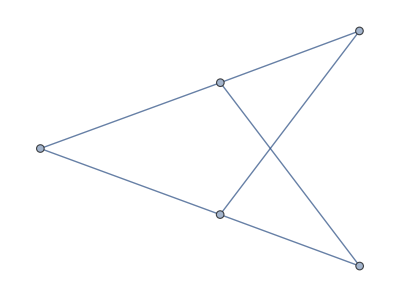

{3,1,4,2,5}

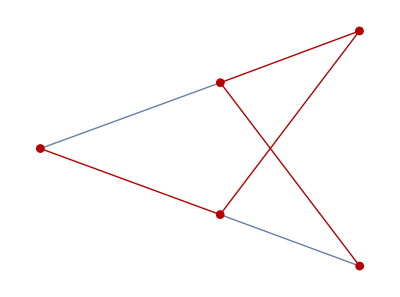

```mathematica
Block[{exp,ag,sq,len,lenag,lensq,graph,allpartitions,range},
exp=test;

(*Split square from angles. The expression comes from a Times so it will already be ordered with angles first*)
{ag,sq}=SplitBy[exp,Head];
len=Length[exp];

(*lenag and lensq will be used as an offset later*)
lenag=Length[ag];
lensq=Length[sq];

graph=AdjacencyGraph@(Join[PadLeft[#,len]&/@(Table[If[FreeQ[sq,Alternatives@@j],0,1],{j,ag},{i,sq}]),
PadRight[#,len]&/@(Table[If[FreeQ[ag,Alternatives@@j],0,1],{j,sq},{i,ag}])])//Echo;
range=Range[len];
FindShortestPath[graph,Sequence@@#]&/@Subsets[Range[len],{2}];
allpartitions=If[OddQ[len],
(*If there are an odd number of brackets we must first isolate some to make it even and apply Rojo's partition function. Then map FindShortestPath on the outcome*)
Table[{{i},partitionsRojo[#,2]&@(Drop[range,{i}])},{i,len}]
];
HighlightGraph[graph,PathGraph@Echo@FindHamiltonianPath[graph]]
]
```

#### Again with Garphs

```mathematica
Block[{exp,ag,sq,len,lenag,lensq,graph,allpartitions,range},
exp=test;

(*Split square from angles. The expression comes from a Times so it will already be ordered with angles first*)
{ag,sq}=SplitBy[exp,Head];
len=Length[exp];

(*lenag and lensq will be used as an offset later*)
lenag=Length[ag];
lensq=Length[sq];

graph=((Join[PadLeft[#,len]&/@(Table[If[FreeQ[sq,Alternatives@@j],0,1],{j,ag},{i,sq}]),
ConstantArray[0,{lensq,len}]]));
graph=AdjacencyGraph@Echo@(graph+Transpose[graph])//Echo;

globalgraph=graph;
range=Range[len];
Table[FindShortestPath[graph,1,i],{i,len}]
]
```

{{0,0,1,1,1},{0,0,1,1,1},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}}

-Graphics-

{{1},{1,3,2},{1,3},{1,4},{1,5}}

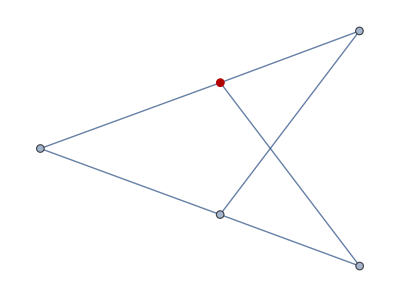
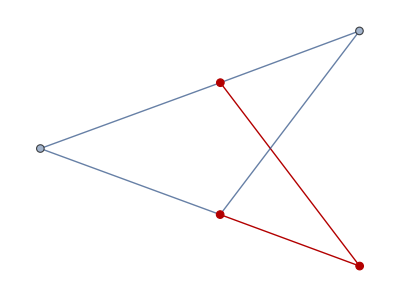
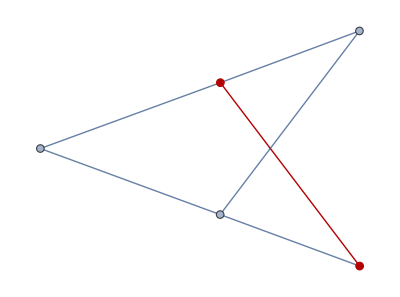
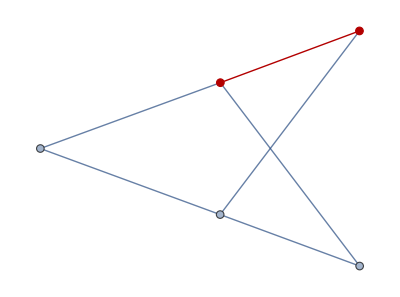
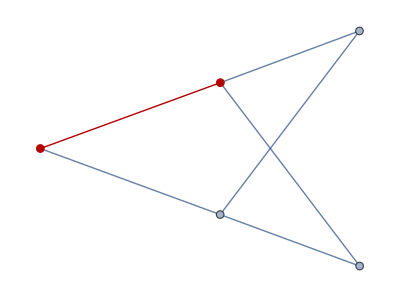

```mathematica
HighlightGraph[globalgraph,PathGraph@#]&/@((Table[FindShortestPath[#3,#1,i],{i,#2}]&@@{First@VertexList[#],VertexList[#],#}&)@globalgraph)
```


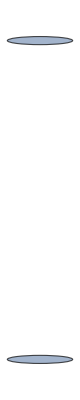

{{{1},-Graphics-},{{1,3,2},-Graphics-},{{1,3},-Graphics-},{{1,4},-Graphics-},{{1,5},-Graphics-}}

```mathematica
{#,VertexDelete[globalgraph,#]}&/@((Table[FindShortestPath[#3,#1,i],{i,#2}]&@@{First@VertexList[#],VertexList[#],#}&)@globalgraph)
```

```mathematica
ftest=FindShortestPath[globalgraph,1,All]
```

ShortestPathFunction[{1,All},«»]

```mathematica
ftest/@VertexList[globalgraph]
```

{{1},{1,3,2},{1,3},{1,4},{1,5}}

```mathematica
FindShortestPath[globalgraph,1,All]/@VertexList[globalgraph]
```

{{1},{1,3,2},{1,3},{1,4},{1,5}}

```mathematica
Table[FindShortestPath[#,i,j],{i,VertexList[#]},{j,VertexList[#]}]&@globalgraph
```

{{{1},{1,3,2},{1,3},{1,4},{1,5}},{{2,3,1},{2},{2,3},{2,4},{2,5}},{{3,1},{3,2},{3},{3,1,4},{3,1,5}},{{4,1},{4,2},{4,1,3},{4},{4,1,5}},{{5,1},{5,2},{5,1,3},{5,1,4},{5}}}

```mathematica
FindHamiltonianCycle[globalgraph]
```

{}

```mathematica
AdjacencyMatrix@globalgraph//Normal//MatrixForm
```

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

```mathematica
Subsets[Range[10],{1,9}]//Length
```

1022

```mathematica
ConstantArray[0,{3,5}]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

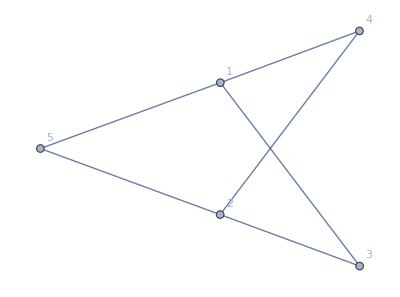

```mathematica
GraphPlot[globalgraph,VertexLabels->"Name"]
```

#### And again

```mathematica
Block[{exp,ag,sq,len,lenag,lensq,graph,agconnections},
exp=test;

(*Split square from angles. The expression comes from a Times so it will already be ordered with angles first*)
{ag,sq}=SplitBy[exp,Head];
len=Length[exp];

(*lenag and lensq will be used as an offset later*)
lenag=Length[ag];
lensq=Length[sq];

(*For each angle bracket we find with which square brackect it can be connected and select a type of connection: 1-⟨i_⟩[i_] 2-⟨_i⟩[i_] 3-⟨i_⟩[_i] 4-⟨_i⟩[_i]*)
agconnections=Table[{{i,j},If[FreeQ[i,Alternatives@@j],0,
Which[
First@@i===First@@j,
1,
Last@@i===First@@j,
2,
First@@i===Last@@j,
3,
Last@@i===Last@@j,
4]]},{i,ag},{j,sq}]


]
```

{{{{12,14},Null},{{12,23},Null},{{12,24},Null}},{{{34,14},1},{{34,23},Null},{{34,24},1}}}

```mathematica
graph=((Join[PadLeft[#,2*len]&/@(Table[If[FreeQ[sq,Alternatives@@j],0,1],{j,ag},{i,sq}]),
ConstantArray[0,{lensq,len}]]))
graph=AdjacencyGraph@Echo@(graph+Transpose[graph])//Echo
```

```mathematica
Table[{i,j},{i,2},{j,{a,b}}]
```

{{{1,a},{1,b}},{{2,a},{2,b}}}

```mathematica
Which[False,
1,
True,
2
]
```

2

```mathematica
Table[Which[False,
1,
True,
2
],{i,4}]
```

{2,2,2,2}

```mathematica
Block[{exp,ag,sq,len,lenag,lensq,graph,agconnections,aglabs,sqlabs},
exp=test;

(*Split square from angles. The expression comes from a Times so it will already be ordered with angles first*)
{ag,sq}=SplitBy[exp,Head];
len=Length[exp];

(*lenag and lensq will be used as an offset later*)
lenag=Length[ag];
lensq=Length[sq];

aglabs=Flatten[List@@@ag];
sqlabs=Flatten[List@@@sq];

Table[{i,j},{i,ag},{j,sq}]//Echo;
{aglabs,sqlabs}//Echo;
Partition[#,2]&@Echo@(Partition[#,2]&/@(PadLeft[#,2*len]&/@Table[If[i===j,1,0],{i,aglabs},{j,sqlabs}]))

]
```

{{{12,14},{12,23},{12,24}},{{34,14},{34,23},{34,24}}}

{{1,2,3,4},{1,4,2,3,2,4}}

{{{0,0},{0,0},{1,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{1,0},{1,0}},{{0,0},{0,0},{0,0},{0,1},{0,0}},{{0,0},{0,0},{0,1},{0,0},{0,1}}}

{{{{0,0},{0,0},{1,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{1,0},{1,0}}},{{{0,0},{0,0},{0,0},{0,1},{0,0}},{{0,0},{0,0},{0,1},{0,0},{0,1}}}}

#### With weighted graphs

```mathematica
(*Use weighted adjaciency matrices with weight corresponding to type of connection*)
```

```mathematica
(*I do not know why but when building the graph from the weighted adjaciency matrix, you need to put ∞ where I wuold usually put zero...*)
```

```mathematica
weight[SpinorAngleBracket[i_,j_],SpinorSquareBracket[k_,l_]]:=Which[i===k,1,j===k,2,i===l,3,j===l,4,True,0]
```

```mathematica
weight[14,24]
```

4

```mathematica
weight[12,34]//RepeatedTiming
```

{1.66337×10^-6,0}

{{0,0,1,2,2},{0,0,4,3,4},{1,4,0,0,0},{2,3,0,0,0},{2,4,0,0,0}}

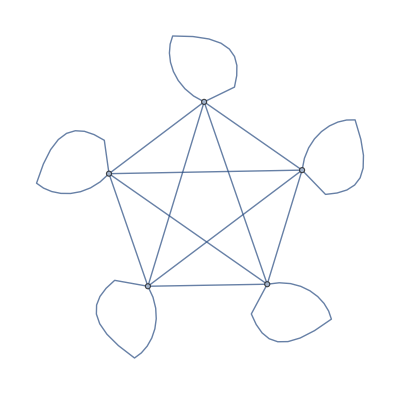

```mathematica
Block[{exp,ag,sq,len,lenag,lensq,graph,allpartitions,range},
exp=test;

(*Split square from angles. The expression comes from a Times so it will already be ordered with angles first*)
{ag,sq}=SplitBy[exp,Head];
len=Length[exp];

(*lenag and lensq will be used as an offset later*)
lenag=Length[ag];
lensq=Length[sq];

graph=((Join[PadLeft[#,len]&/@(Table[weight[j,i],{j,ag},{i,sq}]),
ConstantArray[0,{lensq,len}]]));
graph=WeightedAdjacencyGraph@Echo@(graph+Transpose[graph])//Echo;

globalgraph=graph;
range=Range[len];

]
```

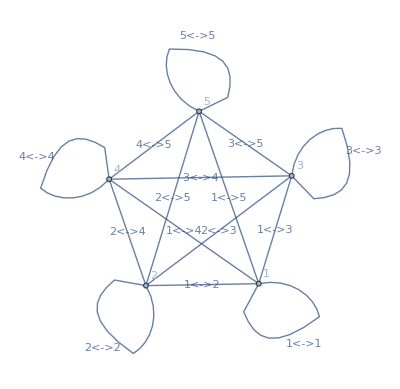

```mathematica
GraphPlot[WeightedAdjacencyGraph[{{0,0,1,2,2},{0,0,4,3,4},{1,4,0,0,0},{2,3,0,0,0},{2,4,0,0,0}}],EdgeLabels->"Name",VertexLabels->"Name"]
```

```mathematica
globalgraph//WeightedAdjacencyMatrix//Normal
```

{{0,0,1,2,2},{0,0,4,3,4},{1,4,0,0,0},{2,3,0,0,0},{2,4,0,0,0}}

#### Other tests

```mathematica
weight[SpinorAngleBracket[i_,j_],SpinorSquareBracket[k_,l_]]:=Which[i===k,1,j===k,2,i===l,3,j===l,4,True,0]
```

```mathematica
(*Modified weight function swapping cases 1 and 3, so that angle test still forbids even cases and square test forbids summing to 5 i.e. the cobination of 1 with 4 and 2 with 3*)
```

```mathematica
weight[SpinorAngleBracket[i_,j_],SpinorSquareBracket[k_,l_]]:=Which[i===k,3,j===k,2,i===l,1,j===l,4,True,0]
```

```mathematica
(*sqtest checks whther all the contractions with the square brackets are possible. In particular you cannot have the same square bracket whose first label contract more than one angle bracket. This is checked by looking at the labels. The implemented test condition proved to be the fasted I could find*)
```

```mathematica
sqtest[exp_List]:=Equal[Length@#,Length@DeleteCases[#,_?(!MatchQ[#,({{i_,j_},{k_,l_}}/;j≠l&&j+l≠5)|{{_,_}}]&)]]&@GatherBy[#,First]&@Flatten[exp,1]
```

```mathematica
Block[{exp,ag,sq,len,lenag,lensq,allcontractions},
exp=test;

(*Split square from angles. The expression comes from a Times so it will already be ordered with angles first*)
{ag,sq}=SplitBy[exp,Head];
len=Length[exp];

(*lenag and lensq will be used as an offset later*)
lenag=Length[ag];
lensq=Length[sq];

(*allcontractions gives all the possible contractions of the angles with the squares. Angles are labelled by row in matrix, squares by explicit label (in order to avoid gigantic matrices) and second label is weight. We remove all the terms signaling no possible contraction*)
allcontractions=DeleteCases[#,{_,0}]&/@Table[{j,weight[i,sq[[j]]]},{i,ag},{j,lensq}]//Echo;
(*Next out of the possible contractions on the single row we take pairs of compatibel contractions, so first take Subsets grouping by 2, then delete those whose associated weight sum is even. The weights have been assigned exactly in such a way that these are the forbidden cases. Then take all the possible combinations of the allowed contractions*)
Tuples@Echo@(DeleteCases[#,{{i_,j_},{k_,l_}}/;EvenQ[j+l]]&@Subsets[#,{2}]&/@allcontractions)
(*Next we need to combine these data back into chains*)
]
```

{{{1,3},{2,2},{3,2}},{{1,4},{2,1},{3,4}}}

{{{{1,3},{2,2}},{{1,3},{3,2}}},{{{1,4},{2,1}},{{2,1},{3,4}}}}

{{{{1,3},{2,2}},{{1,4},{2,1}}},{{{1,3},{2,2}},{{2,1},{3,4}}},{{{1,3},{3,2}},{{1,4},{2,1}}},{{{1,3},{3,2}},{{2,1},{3,4}}}}

```mathematica
sqtest/@%//RepeatedTiming
```

{0.0000542993,{True,True,True,True}}

```mathematica
DeleteCases[#,{{i_,j_},{k_,l_}}/;EvenQ[j+l]]&@Subsets[{{1,1},{2,2},{3,2}},{2}]//RepeatedTiming
```

{5.13978×10^-6,{{{1,1},{2,2}},{{1,1},{3,2}}}}

```mathematica
DeleteCases[#,_?(EvenQ[Total@Last@Transpose@#]&)]&@Subsets[{{1,1},{2,2},{3,2}},{2}]//RepeatedTiming
```

{0.000022526,{{{1,1},{2,2}},{{1,1},{3,2}}}}

```mathematica
(*First option is faster*)
```

```mathematica
Tuples[{{{{1,1},{2,2}},{{1,1},{3,2}}},{{{1,4},{2,3}},{{2,3},{3,4}}}}]
```

{{{{1,1},{2,2}},{{1,4},{2,3}}},{{{1,1},{2,2}},{{2,3},{3,4}}},{{{1,1},{3,2}},{{1,4},{2,3}}},{{{1,1},{3,2}},{{2,3},{3,4}}}}

```mathematica
test
```

{12,34,14,23,24}

```mathematica
DeleteDuplicatesBy[#,_?(Abs[Last@#1-Last@#2]==1&)]&@Flatten[{{{1,1},{2,2}},{{1,4},{2,3}},{},{},{{1,2},{5,3}}},1]
```

{{1,1},{2,2},{1,4},{2,3},{1,2},{5,3}}

```mathematica
DeleteCases[#,_?(Length[#]>2&)]&@GatherBy[#,First]&@Flatten[{{{1,1},{2,2}},{{1,4},{2,3}},{},{},{{1,2},{5,3}}},1]//RepeatedTiming
```

{7.21049×10^-6,{{{2,2},{2,3}},{{5,3}}}}

```mathematica
DeleteCases[#,_?(MatchQ[Plus@@#,{_,5}]&)]&@GatherBy[#,First]&@Flatten[{{{1,1},{2,2}},{{1,4},{2,3}},{},{},{{1,2},{5,3}}},1]//RepeatedTiming
```

{9.97078×10^-6,{{{1,1},{1,4},{1,2}},{{5,3}}}}

```mathematica
DeleteCases[#,_?(Length[#]>2||MatchQ[Plus@@#,{_,5}]&)]&@GatherBy[#,First]&@Flatten[{{{1,1},{2,2}},{{1,4},{2,3}},{},{},{{1,2},{5,3}}},1]//RepeatedTiming
```

{0.0000109958,{{{5,3}}}}

```mathematica
DeleteCases[#,_?(MatchQ[Plus@@#,{_,5}]&)]&@DeleteCases[#,_?(Length[#]>2&)]&@GatherBy[#,First]&@Flatten[{{{1,1},{2,2}},{{1,4},{2,3}},{},{},{{1,2},{5,3}}},1]//RepeatedTiming
```

{0.0000115131,{{{5,3}}}}

```mathematica
GatherBy[#,First]&@Flatten[{{{1,1},{2,2}},{{1,4},{2,3}},{},{},{{1,2},{5,3}},{{6,1},{6,2}}},1]
```

{{{1,1},{1,4},{1,2}},{{2,2},{2,3}},{{5,3}},{{6,1},{6,2}}}

```mathematica
DeleteCases[#,_?(!MatchQ[#,({{i_,j_},{k_,l_}}/;j+l≠5)|{{_,_}}]&)]&@GatherBy[#,First]&@Flatten[{{{1,1},{2,2}},{{1,4},{2,3}},{},{},{{1,2},{5,3}},{{6,1},{6,2}}},1]//RepeatedTiming
```

{0.0000114714,{{{5,3}},{{6,1},{6,2}}}}

```mathematica
sqtest[exp_List]:=Equal[Length@#,Length@DeleteCases[#,_?(Length[#]>2||MatchQ[Plus@@#,{_,5}]&)]]&@GatherBy[#,First]&@Flatten[exp,1]
```

```mathematica
(*Now the pairing*)
```

```mathematica
{{{{1,3},{2,2}},{{1,3},{3,2}}},{{{1,4},{2,1}},{{2,1},{3,4}}}}
```

```mathematica
pairing[x_,y_]:=If[sqtest[#],#,Nothing[]]&@Join[x,{y}]
```

```mathematica
pairing[{{{1,3},{2,2}}},{{1,4},{2,1}}]
```

{{{1,3},{2,2}},{{1,4},{2,1}}}

```mathematica
Length@Fold[Flatten[Outer[pairing,#1,#2,1],1]&,{{{{1,3},{2,2}}},{{{1,3},{3,2}}}},{{{{1,4},{2,1}},{{2,1},{3,4}}},{{{1,3},{6,1}},{{6,1},{6,3}}}}]//RepeatedTiming
```

{0.000166094,4}

```mathematica
Length@Tuples[{{{{1,3},{2,2}},{{1,3},{3,2}}},{{{1,4},{2,1}},{{2,1},{3,4}}},{{{1,3},{6,1}},{{6,1},{6,3}}}}]//RepeatedTiming
```

{2.53386×10^-6,8}

```mathematica
Outer[pairing,{{{{1,3},{2,2}},{{1,4},{2,1}}},{{{1,3},{2,2}},{{2,1},{3,4}}},{{{1,3},{3,2}},{{1,4},{2,1}}},{{{1,3},{3,2}},{{2,1},{3,4}}}},{{{1,3},{6,1}}},1]
```

{{},{{{{1,3},{2,2}},{{2,1},{3,4}},{{1,3},{6,1}}}},{},{{{{1,3},{3,2}},{{2,1},{3,4}},{{1,3},{6,1}}}}}

```mathematica
pairing[{{{1,3},{2,2}},{{2,1},{3,4}}},{{1,3},{6,1}}]
```

{{{1,3},{2,2}},{{2,1},{3,4}},{{1,3},{6,1}}}

```mathematica
sqtest[{{{1,3},{2,2}},{{2,1},{3,4}},{{1,3},{6,1}}}]
```

True

```mathematica
Equal[Length@#,Length@DeleteCases[#,_?(!MatchQ[#,({{i_,j_},{k_,l_}}/;j≠l&&j+l≠5)|{{_,_}}]&)]]&@Echo@GatherBy[#,First]&@Flatten[{{{1,3},{2,2}},{{2,1},{3,4}},{{6,1},{6,3}}},1]
```

{{{1,3}},{{2,2},{2,1}},{{3,4}},{{6,1},{6,3}}}

True

```mathematica
FoldList[Flatten[Outer[pairing,#1,#2,1],1]&,{{{{1,3},{2,2}}},{{{1,3},{3,2}}}},{{{{1,4},{2,1}},{{2,1},{3,4}}}}]//RepeatedTiming
```

{0.0000499031,{{{{{1,3},{2,2}}},{{{1,3},{3,2}}}},{{{{1,3},{2,2}},{{1,4},{2,1}}},{{{1,3},{2,2}},{{2,1},{3,4}}},{{{1,3},{3,2}},{{1,4},{2,1}}},{{{1,3},{3,2}},{{2,1},{3,4}}}}}}

```mathematica
Tuples@{{{{1,3},{2,2}},{{1,3},{3,2}}},{{{1,4},{2,1}},{{2,1},{3,4}}}}//RepeatedTiming
```

{1.81403×10^-6,{{{{1,3},{2,2}},{{1,4},{2,1}}},{{{1,3},{2,2}},{{2,1},{3,4}}},{{{1,3},{3,2}},{{1,4},{2,1}}},{{{1,3},{3,2}},{{2,1},{3,4}}}}}

```mathematica
FoldList[Outer[g,#1,#2,1]&,{{x}},{{y},{z}}]
```

{{{x}},{{g[{x},y]}},{{g[{g[{x},y]},z]}}}

```mathematica
Outer[g,{1,2},{{a},b},1]
```

{{g[1,{a}],g[1,b]},{g[2,{a}],g[2,b]}}

```mathematica
Fold[Flatten[Outer[pairing,#1,#2,1],1]&,{{{{1,3},{2,2}}},{{{1,3},{3,2}}}},{{{{1,4},{2,1}},{{2,1},{3,4}}},{{{1,3},{6,1}},{{6,1},{6,3}}}}]
```

```mathematica
g[{#}&/@(First@#),#[[2;;]]]&@{{{{1,3},{2,2}},{{1,3},{3,2}}},{{{1,4},{2,1}},{{2,1},{3,4}}},{{{1,3},{6,1}},{{6,1},{6,3}}}}
```

g[{{{{1,3},{2,2}}},{{{1,3},{3,2}}}},{{{{1,4},{2,1}},{{2,1},{3,4}}},{{{1,3},{6,1}},{{6,1},{6,3}}}}]

```mathematica
{{{{1,3},{2,2}},{{1,3},{3,2}}},{{{1,4},{2,1}},{{2,1},{3,4}}},{{{1,3},{6,1}},{{6,1},{6,3}}}}Fold[(Flatten[Outer[pairing,#1,#2,1],1]&),{#}&/@(First@#),#[[2;;]]]&@%
```

Thread::tdlen: Objects of unequal length in {{{{1,3},{2,2}},{{1,3},{3,2}}},{{{1,4},{2,1}},{{2,1},{3,4}}},{{{1,3},{6,1}},{{6,1},{6,3}}}} {} cannot be combined.

{} {{{{1,3},{2,2}},{{1,3},{3,2}}},{{{1,4},{2,1}},{{2,1},{3,4}}},{{{1,3},{6,1}},{{6,1},{6,3}}}}

```mathematica
allpairings[exp_List]:=Fold[Flatten[Outer[pairing,#1,#2,1],1]&,{#}&/@(First@exp),exp[[2;;]]]
```

```mathematica
prova={{{{1,3},{2,2}},{{1,3},{3,2}}},{{{1,4},{2,1}},{{2,1},{3,4}}},{{{1,3},{6,1}},{{6,1},{6,3}}}};
```

```mathematica
allpairings[prova]//RepeatedTiming
```

{0.000175118,{{{{1,3},{2,2}},{{1,4},{2,1}},{{6,1},{6,3}}},{{{1,3},{2,2}},{{2,1},{3,4}},{{6,1},{6,3}}},{{{1,3},{3,2}},{{1,4},{2,1}},{{6,1},{6,3}}},{{{1,3},{3,2}},{{2,1},{3,4}},{{6,1},{6,3}}}}}

#### Auxiliary

```mathematica
weight[SpinorAngleBracket[i_,j_],SpinorSquareBracket[k_,l_]]:=Which[i===k,1,j===k,2,i===l,3,j===l,4,True,0]
```

```mathematica
(*Modified weight function swapping cases 1 and 3, so that angle test still forbids even cases and square test forbids summing to 5 i.e. the cobination of 1 with 4 and 2 with 3*)
```

```mathematica
weight[SpinorAngleBracket[i_,j_],SpinorSquareBracket[k_,l_]]:=Which[i===k,3,j===k,2,i===l,1,j===l,4,True,0]
```

```mathematica
(*sqtest checks whther all the contractions with the square brackets are possible. In particular you cannot have the same square bracket whose first label contract more than one angle bracket. This is checked by looking at the labels. The implemented test condition proved to be the fasted I could find*)
```

```mathematica
sqtest[exp_List]:=Equal[Length@#,Length@DeleteCases[#,_?(!MatchQ[#,({{i_,j_},{k_,l_}}/;j≠l&&j+l≠5)|{{_,_}}]&)]]&@GatherBy[#,First]&@Flatten[exp,1]
```

```mathematica
(*The next functions build all the possible pairings of contractions testing the square brackets. I use Outer instead of Tuples because like this I can perform the test at each step and not just at the end. For large number of possible contractions with many cancellations this should speed up the process. In simple cases it might be slower*)
```

```mathematica
pairing[x_,y_]:=If[sqtest[#],#,Nothing[]]&@Join[x,{y}]
```

```mathematica
allpairings[exp_List]:=Fold[Flatten[Outer[pairing,#1,#2,1],1]&,{#}&/@(First@exp),exp[[2;;]]]
```

```mathematica
(*allpairings again with Tuples an dcheck at the end*)
```

```mathematica
allpairingsTuples[exp_List]:=DeleteCases[Tuples@exp,_?(!sqtest[#]&)]
```

```mathematica
prova={{{{1,3},{2,2}},{{1,3},{3,2}}},{{{1,4},{2,1}},{{2,1},{3,4}}},{{{1,3},{6,1}},{{6,1},{6,3}}}};
```

```mathematica
allpairings[prova]//RepeatedTiming
```

{0.000179067,{{{{1,3},{2,2}},{{1,4},{2,1}},{{6,1},{6,3}}},{{{1,3},{2,2}},{{2,1},{3,4}},{{6,1},{6,3}}},{{{1,3},{3,2}},{{1,4},{2,1}},{{6,1},{6,3}}},{{{1,3},{3,2}},{{2,1},{3,4}},{{6,1},{6,3}}}}}

```mathematica
allpairingsTuples[prova]//RepeatedTiming
```

{0.000149118,{{{{1,3},{2,2}},{{1,4},{2,1}},{{6,1},{6,3}}},{{{1,3},{2,2}},{{2,1},{3,4}},{{6,1},{6,3}}},{{{1,3},{3,2}},{{1,4},{2,1}},{{6,1},{6,3}}},{{{1,3},{3,2}},{{2,1},{3,4}},{{6,1},{6,3}}}}}

```mathematica
test={12,34,14,23,24}
```

{12,34,14,23,24}

```mathematica
Block[{exp,ag,sq,len,lenag,lensq,allchains,local,array},
exp=test;

(*Split square from angles. The expression comes from a Times so it will already be ordered with angles first*)
{ag,sq}=SplitBy[exp,Head];
len=Length[exp];

(*lenag and lensq will be used as an offset later*)
lenag=Length[ag];
lensq=Length[sq];

(*allcontractions gives all the possible contractions of the angles with the squares. Angles are labelled by row in matrix, squares by explicit label (in order to avoid gigantic matrices) and second label is weight. We remove all the terms signaling no possible contraction*)
allcontractions=DeleteCases[#,{_,0}]&/@Table[{j,weight[i,sq[[j]]]},{i,ag},{j,lensq}]//Echo;
(*Next out of the possible contractions on the single row we take pairs of compatibel contractions, so first take Subsets grouping by 2, then delete those whose associated weight sum is even. The weights have been assigned exactly in such a way that these are the forbidden cases. Then take all the possible combinations of the allowed contractions*)
allchains=allpairings@Echo@(DeleteCases[#,{{i_,j_},{k_,l_}}/;EvenQ[j+l]]&@Subsets[#,{2}]&/@allcontractions)

(*Next we need to combine these data back into chains*)
(*local=First@allchains;
array={};
Do[array=Join[array,{{i,First@j}->Last@j}];

,{i,Length[local]},{j,local[[i]]}];
WeightedAdjacencyGraph[(Normal@Join[(PadRight[#,5]&/@SparseArray@array),ConstantArray[0,{3,5}]])/.{0->∞}]*)

]
```

{{{1,3},{2,2},{3,2}},{{1,4},{2,1},{3,4}}}

{{{{1,3},{2,2}},{{1,3},{3,2}}},{{{1,4},{2,1}},{{2,1},{3,4}}}}

{{{{1,3},{2,2}},{{1,4},{2,1}}},{{{1,3},{2,2}},{{2,1},{3,4}}},{{{1,3},{3,2}},{{1,4},{2,1}}},{{{1,3},{3,2}},{{2,1},{3,4}}}}

```mathematica
prova=%;
```

#### Backcontracting lists into chains

```mathematica
test={12,34,56,14,23,24}
```

{12,34,56,14,23,24}

```mathematica
prova[[1]]
```

{{{1,3},{2,2}},{{1,4},{2,1}}}

```mathematica
Block[{ang,squ,exp,locexp,locexp2,start,chain},
ang={12,34,56};
squ={14,23,24};
exp=prova[[1]];

(*Add in the labels for the angle brackets and flatten*)
locexp=Flatten[Table[Join[{i},#]&/@exp[[i]],{i,Length[exp]}],1]//Echo;

(*Find a starting point. If there is a list with single contraction then start with that angle, else look for a square with single contraction, if neither is found then this is a trace and we pick as starting point the first angle in the bracket list.*)
Which[Length@(start=Position[exp,_?(Length[#]==1&)])>1,
(*There is a non-empty angle starting point, we pick the first of them*)
start=start[[1,1]];



];


]
```

{{1,1,3},{1,2,2},{2,1,4},{2,2,1}}

```mathematica
Position[{{{1,3},{2,2}},{{1,4},{2,1}},{{5,2}},{{6,1}}},_?(Length[#]==1&)]
```

{{3},{4}}

### Minimal Chains

#### Auxiliary

```mathematica
(*Modified weight function swapping cases 1 and 3, so that angle test still forbids even cases and square test forbids summing to 5 i.e. the cobination of 1 with 4 and 2 with 3*)
```

```mathematica
weight[SpinorAngleBracket[i_,j_],SpinorSquareBracket[k_,l_]]:=Which[i===k,3,j===k,2,i===l,1,j===l,4,True,0]
```

```mathematica
(*sqtest checks whther all the contractions with the square brackets are possible. In particular you cannot have the same square bracket whose first label contract more than one angle bracket. This is checked by looking at the labels. The implemented test condition proved to be the fasted I could find*)
```

```mathematica
sqtest[exp_List]:=Equal[Length@#,Length@DeleteCases[#,_?(!MatchQ[#,({{_,i_,j_},{_,k_,l_}}/;j≠l&&j+l≠5)|{{_,_,_}}]&)]]&@GatherBy[#,Part[#,2]&]&@Flatten[exp,1]
```

```mathematica
(*The next functions build all the possible pairings of contractions testing the square brackets. I use Outer instead of Tuples because like this I can perform the test at each step and not just at the end. For large number of possible contractions with many cancellations this should speed up the process. In simple cases it might be slower*)
```

```mathematica
pairing[x_,y_]:=If[sqtest[#],#,Nothing[]]&@Join[x,{y}]
```

```mathematica
allpairings[exp_List]:=Fold[Flatten[Outer[pairing,#1,#2,1],1]&,{#}&/@(First@exp),exp[[2;;]]]
```

```mathematica
(*allpairings again with Tuples an dcheck at the end*)
```

```mathematica
allpairingsTuples[exp_List]:=DeleteCases[Tuples@exp,_?(!sqtest[#]&)]
```

#### Chains in list form

```mathematica
test={12,56,34,14,23,24}
```

{12,56,34,14,23,24}

```mathematica
chainLists[exp_List]:=Block[{ag,sq,len,lenag,lensq,allchains,local},

(*Split square from angles. The expression comes from a Times so it will already be ordered with angles first*)
{ag,sq}=SplitBy[exp,Head];
len=Length[exp];

(*lenag and lensq will be used as an offset later*)
lenag=Length[ag];
lensq=Length[sq];

(*allcontractions gives all the possible contractions of the angles with the squares. Angles are labelled by row in matrix, squares by explicit label (in order to avoid gigantic matrices) and second label is weight. We remove all the terms signaling no possible contraction*)
allchains=DeleteCases[#,{}]&@(DeleteCases[#,{_,_,0}]&/@Table[{i,j,weight[ag[[i]],sq[[j]]]},{i,lenag},{j,lensq}]);
(*Next out of the possible contractions on the single row we take pairs of compatibel contractions, so first take Subsets grouping by 2, then delete those whose associated weight sum is even. The weights have been assigned exactly in such a way that these are the forbidden cases. Then take all the possible combinations of the allowed contractions*)

allchains=If[Length[#]>1,Subsets[#,{2}],{#}]&/@allchains;

allchains=Flatten[#,1]&/@allpairings@(DeleteCases[#,{{_,_,j_},{_,_,l_}}/;EvenQ[j+l]]&/@allchains);
Return[allchains];

];
```

```mathematica
test
```

{12,56,34,14,23,24}

```mathematica
chainLists[test]
```

{{{1,1,3},{1,2,2},{3,1,4},{3,2,1}},{{1,1,3},{1,2,2},{3,2,1},{3,3,4}},{{1,1,3},{1,3,2},{3,1,4},{3,2,1}},{{1,1,3},{1,3,2},{3,2,1},{3,3,4}}}

```mathematica
prova=%;
```

```mathematica
test1={12,56,23,67}
prova=chainLists[%]
```

{12,56,23,67}

{{{1,1,2},{2,2,2}}}

```mathematica
test
```

{12,56,34,14,23,24}

```mathematica
chainLists[test]//RepeatedTiming
```

{0.000156035,{{{1,1,3},{1,2,2},{3,1,4},{3,2,1}},{{1,1,3},{1,2,2},{3,2,1},{3,3,4}},{{1,1,3},{1,3,2},{3,1,4},{3,2,1}},{{1,1,3},{1,3,2},{3,2,1},{3,3,4}}}}

#### From lists to actual chains

```mathematica
test
```

{12,56,34,14,23,24}

```mathematica
test1={12,56,23,67}
prova=chainLists[%]
```

{12,56,23,67}

{{{1,1,2},{2,2,2}}}

```mathematica
Block[{ang,squ,exp,agstart,sqstart,localstart,chains,localchain,next,sign,type},


exp=prova[[1]]//Echo;

(*Not external data, get modified later on*)
{ang,squ}=GatherBy[test1,Head];
(*Convert brackets into lists of arguments*)
ang=List@@@ang;
squ=List@@@squ;

(*Find a starting point. If there is a list with single contraction then start with that angle, else look for a square with single contraction, if neither is found then this is a trace and we pick as starting point the first angle in the bracket list.*)

{agstart,sqstart}=Map[First,#,{2}]&@(Select[#,(Last[#]==1&)]&/@(Tally/@((Transpose@exp)[[;;2]])));

(*First we address the angle starting points, then the squares, and once all those are done we build the traces (what is left has the no helicity so must be traces)*)

chains={};
(*TO BE LOOPED*)
While[Length[agstart]>0,
localstart=First@agstart//Echo;
next=First@Cases[exp,{localstart,_,_},1,1]//Echo;
sign=1;
localchain={};
(*As long as there is a next bracket keep looping*)
While[True,
type=Last@next;
(*THIS SELECTION OF THE ORDERING IS PROBABLY WRONG, THE ORDERING DEPENDS ON WHETHER WE ARE LOOKING FOR AN ANGLE OR SQUARE BRACKET NEXT*)
Which[type==1,
localchain=Join[localchain,Reverse[ang[[First@next]]]],
type==2,
localchain=Join[localchain,ang[[First@next]]],
type==3,
localchain=Join[localchain,Reverse[ang[[First@next]]]];
sign=-1*sign,
type==4,
localchain=Join[localchain,ang[[First@next]]];
sign=-1*sign;
];

(*Now we need to select the next bracket. This depends on whether we are looking for an angle or a square.*)
If[OddQ[Length[localchain]],
(*On the odd iterations we are looking for a next angle bracket*)
localstart=next;
next=First@Cases[exp,{_,next[[2]],_},1,1];
(*If there is no bracket break the While and build the chain*)
If[Length[next]==0,
localchain=Flatten[localchain];
(*build the chain. Sign of possible reordering already accounted for*)
If[Equal[Last@localstart,1|4],
chains=Join[chains,{sign*Chain[$angle,First@localchain,localchain[[2;;]],Last@squ[[localstart[[2]]]],$square]}];
,
chains=Join[chains,{sign*Chain[$angle,First@localchain,localchain[[2;;]],First@squ[[localstart[[2]]]],$square]}];
];

Break[];
];
,
(*On the even iterations we look*)

];

Break[]
];

Break[]

];


(*This must be looped until no chains can be possibly made*)


]
```

{{1,1,2},{2,2,2}}

{{1,2},{1,2}}

1

{1,1,2}

```mathematica
(*DIFFERENT APPROACH: I COULD JUST START FROM A GIVEN BRACKET, PUT IT INTO A LIST AND THEN APPEND BRACKETS LEFT AND RIGHT BASED ON WHERE THESE ARE ATTACHED AND SEUBSEQUENTLY REMOVING THE PERFORMED CONTRACTION FROM THE LIST OF CONTRACTIONS*)
```

```mathematica
Take[{1,2,3},UpTo[5]]
```

{1,2,3}

```mathematica
Range[10];
DeleteCases[%,3]//RepeatedTiming
```

{2.38526×10^-6,{1,2,4,5,6,7,8,9,10}}

```mathematica
Range[10];
Complement[%,{3}]//RepeatedTiming
```

{1.81079×10^-6,{1,2,4,5,6,7,8,9,10}}

```mathematica
aptest={1,2,3};
AppendTo[aptest,4]//RepeatedTiming
```

{0.0000858452,{1,2,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,32588,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}}
 |  |  |  |

```mathematica
Join[{1,2,3},{4}]//RepeatedTiming
```

{1.96788×10^-7,{1,2,3,4}}

```mathematica
Range[10];
MemberQ[%,9]//RepeatedTiming
```

{1.88511×10^-6,True}

```mathematica
Take[{},UpTo[1]]
```

{}

```mathematica
Cases[{{1,1,2},{2,2,2},{1,1,3}},{1,x_,y_}:>{x,y},1,1]
```

{{1,2}}

```mathematica
{ts1,ts2}={}
```

Set::shape: Lists {ts1,ts2} and {} are not the same shape.

{}

```mathematica
?Equal
```

#### Testing something different

```mathematica
chtest /: List[x___,chtest[{i_,j_,k_}],y___,chtest[{q_,j_,l_}],z___]:=List[x,chtest[{i,j,k}],chtest[q,j,l],y,z];
chtest /: List[x___,chtest[{i_,j_,k_}],y___,chtest[{i_,q_,l_}],z___]:=List[x,chtest[{i,j,k}],chtest[i,q,l],y,z];
```

```mathematica
{{{1,1,3},{1,2,2},{3,1,4},{3,2,1}},{{1,1,3},{1,2,2},{3,2,1},{3,3,4}},{{1,1,3},{1,3,2},{3,1,4},{3,2,1}},{{1,1,3},{1,3,2},{3,2,1},{3,3,4}}}
```

```mathematica
{{1,1,3},{1,2,2},{3,1,4},{3,2,1}}
chtest/@%
```

{{1,1,3},{1,2,2},{3,1,4},{3,2,1}}

{chtest[{1,1,3}],chtest[1,2,2],chtest[3,1,4],chtest[3,2,1]}

```mathematica
Clear[chtest]
```

```mathematica
pr={{1,1,3},{1,2,2},{3,1,4},{3,2,1}}
```

{{1,1,3},{1,2,2},{3,1,4},{3,2,1}}

```mathematica
(*chtest reorders the terms*)
```

```mathematica
(*Pair up everything by contracted square brackets*)
chtest /: List[x1___,chtest[{i_,j_,k_}],x2___,chtest[{q_,j_,l_}],x3___]:=List[x1,x2,x3,chtest[{i,j,k},{q,j,l}]];
(*Further connect by contracted angles*)
chtest /: List[x1___,chtest[{i_,j_,k_},y1___],x2___,chtest[{i_,q_,l_},y2___],x3___]:=List[x1,x2,x3,chtest[Sequence@@Reverse[{y2}],{i,q,l},{i,j,k},y1]];
chtest /: List[x1___,chtest[y1___,{i_,j_,k_}],x2___,chtest[{i_,q_,l_},y2___],x3___]:=List[x1,x2,x3,chtest[y1,{i,j,k},{i,q,l},y2]];
chtest /: List[x1___,chtest[{i_,q_,l_},y2___],x2___,chtest[y1___,{i_,j_,k_}],x3___]:=List[x1,x2,x3,chtest[y1,{i,j,k},{i,q,l},y2]];
chtest /: List[x1___,chtest[y1___,{i_,j_,k_}],x2___,chtest[y2___,{i_,q_,l_}],x3___]:=List[x1,x2,x3,chtest[y1,{i,j,k},{i,q,l},Sequence@@Reverse[{y2}]]];
```

```mathematica
pr
chtest/@pr
```

{{1,1,3},{1,2,2},{3,1,4},{3,2,1}}

{chtest[{3,2,1},{1,2,2},{1,1,3},{3,1,4}]}

```mathematica
{{{1,1,3},{1,2,2},{3,1,4},{3,2,1}},{{1,1,3},{1,2,2},{3,2,1},{3,3,4}},{{1,1,3},{1,3,2},{3,1,4},{3,2,1}},{{1,1,3},{1,3,2},{3,2,1},{3,3,4}}};
Table[chtest/@i,{i,%}]//RepeatedTiming
```

{0.0000921243,{{chtest[{3,2,1},{1,2,2},{1,1,3},{3,1,4}]},{chtest[{1,1,3},{1,2,2},{3,2,1},{3,3,4}]},{chtest[{1,3,2},{1,1,3},{3,1,4},{3,2,1}]},{chtest[{1,1,3},{1,3,2},{3,3,4},{3,2,1}]}}}

```mathematica
(*If chtests starts with two terms like {_,i,_},{_,i,_} then the first entry of the chain is an angle, if it is like {i,_,_},{i,_,_} then it is a square*)
```

```mathematica
Block[{exp,agbrackets,sqbrackets,type1,type2,locexp,first,last},
exp=List[{3,2,1},{1,2,2},{1,1,3}];
agbrackets=List@@@{12,56,34,24};
sqbrackets=List@@@{14,23,24};

(*Find type of the first entry and extract information accordingly*)
If[exp[[1,1]]==exp[[2,1]],
type1=$square;
(*Since square chains are by construction method always even this also terminates with square*)
type2=$square;
(*First entry of the chain*)
first=First@exp;
first=If[Last@first==2||Last@first==3,
Last@sqbrackets[[first[[2]]]],
First@sqbrackets[[first[[2]]]]
];
(*build internal chain*)
locexp={};
Do[
locexp=Join[locexp,If[Last@i==2||Last@i==4,agbrackets[[First@i]],Reverse@(agbrackets[[First@i]])]];
,{i,Last@Transpose@Partition[exp,2]}];
(*Extract last entry of chain. Recall that chains starting with square are always even in length.*)
last=Last@exp;
last=If[Last@last==2||Last@last==3,
Last@sqbrackets[[last[[2]]]],
First@sqbrackets[[last[[2]]]]
];
,
type1=$angle;

(*First entry of the chain*)
first=First@exp;
first=If[Last@first==1||Last@first==3,
Last@agbrackets[[first[[1]]]],
First@agbrackets[[first[[1]]]]
];
first//Echo;
(*build internal chain*)
locexp={};
exp//Echo;
Do[
locexp=Join[locexp,If[Last@i==1||Last@i==4,sqbrackets[[i[[2]]]],Reverse@(sqbrackets[[i[[2]]]])]]//Echo;
,{i,Echo@Last@Transpose@Partition[exp,2]}];

(*Angle chains can be even ⟨...⟩ or odd ⟨...], in the former case we need still to get the last entry of the chain. In the latter case it is the last term in locexp. Notice that traces, despite being of the odd form have an even representation, so these need a separate account*)
If[OddQ[Length[exp]],
type2=$square;
last=Last@locexp;
locexp=Most@locexp;
,
type2=$angle;
(*Extract last entry of chain.*)
last=Last@exp;
last=If[Last@last==1||Last@last==3,
Last@agbrackets[[last[[1]]]],
First@agbrackets[[last[[1]]]]
];
];


];
locexp//Echo;

(*If the number of entries is even then we have either [...] or ⟨...⟩ and extracting information is simple. If it is odd we take the simple even case and add an extra piece. Because of how we built things off terms always start with an angle*)

(-1)^Count[{Last/@exp},3|4,∞]*Chain[type1,first,locexp,last,type2]
]
```

4

{{3,2,1},{1,2,2},{1,1,3}}

{{1,2,2}}

{3,2}

{3}

-4{3}2

```mathematica
Table[i,{i,1,12,2}]
```

{1,3,5,7,9,11}

```mathematica
First@Transpose@Partition[Range[10],2]
```

{1,3,5,7,9}

#### Once more, with feeling

```mathematica
{{chtest[{3,2,1},{1,2,2},{1,1,3},{3,1,4}]},{chtest[{1,1,3},{1,2,2},{3,2,1},{3,3,4}]},{chtest[{1,3,2},{1,1,3},{3,1,4},{3,2,1}]},{chtest[{1,1,3},{1,3,2},{3,3,4},{3,2,1}]}}}
```

```mathematica
Block[{exp,agbrackets,sqbrackets,locexp,type1,type2,chain},
exp={{3,2,1},{1,2,2},{1,1,3},{3,1,4}};
agbrackets=List@@@{12,56,34,24};
sqbrackets=List@@@{14,23,24};
locexp=Transpose@({Part[agbrackets,#1],Part[sqbrackets,#2],#3}&@@Transpose@exp)//Echo;

(*See who starts the chain, angle or square and proceed accordingly*)
If[exp[[1,1]]==exp[[2,1]],
type1=$square;
(*squares only start the chain when they also finish it*)
type2=$square;
(*Pick only the square brackets of the relevant pieces, the beginning and then one every two contractions. Order is given by the contraction type. Recall that the first contraction is different from the rest (due to the skipping of the non-relevant terms)*)
chain=Drop[#,{3,Length[exp],2}]&@(Drop[#,1]&/@locexp);
chain=Flatten@{If[Last@#==2||Last@#==3,Reverse@First@#,First@#]&@First@chain,If[Last@#==1||Last@#==4,Reverse@First@#,First@#]&/@Rest@chain};
,
type1=$angle;
(*Angle chains can be even or odd in the number of contractions, so we distinguish these cases. Also, traces can be represented by odd contractions but appear as even due to their cyclicity, so we have to rewrite them*)
If[EvenQ[Length[exp]]&&First@Last@exp==First@First@exp,
locexp=Most@locexp//Echo;
];

(*If we are dealing with a genuinely even chain just procede as in the square case, in the odd case we are missing the information about the last square chain*)
chain=Drop[#,{3,Length[locexp],2}]&@(Drop[#,{2}]&/@locexp);
chain=Echo@Flatten@{If[Last@#==1||Last@#==3,Reverse@First@#,First@#]&@First@chain,If[Last@#==2||Last@#==4,Reverse@First@#,First@#]&/@Rest@chain};

If[EvenQ[Length[locexp]],
type2=$angle;
,
type2=$square;
chain=Flatten@{chain,If[Last@Last@locexp==2||Last@Last@locexp==3,locexp[[-1,2,2]],locexp[[-1,2,1]]]};
];

];

(*The sign is given by counting the number of swaps in exp*)
(-1)^Count[{Last/@exp},3|4,∞]*Chain[type1,First@chain,chain[[2;;-2]],Last@chain,type2]
]
```

{{{3,4},{2,3},1},{{1,2},{2,3},2},{{1,2},{1,4},3},{{3,4},{1,4},4}}

{{{3,4},{2,3},1},{{1,2},{2,3},2},{{1,2},{1,4},3}}

{4,3,2,1}

4{3,2,1}4

```mathematica
listToChain[exp_List,ag_List,sq_List]:=Module[{agbrackets,sqbrackets,locexp,type1,type2,chain},
agbrackets=List@@@ag;
sqbrackets=List@@@sq;
locexp=Transpose@({Part[agbrackets,#1],Part[sqbrackets,#2],#3}&@@Transpose@exp);

(*See who starts the chain, angle or square and proceed accordingly*)
If[exp[[1,1]]==exp[[2,1]],
type1=$square;
(*squares only start the chain when they also finish it*)
type2=$square;
(*Pick only the square brackets of the relevant pieces, the beginning and then one every two contractions. Order is given by the contraction type. Recall that the first contraction is different from the rest (due to the skipping of the non-relevant terms)*)
chain=Drop[#,{3,Length[exp],2}]&@(Drop[#,1]&/@locexp);
chain=Flatten@{If[Last@#==2||Last@#==3,Reverse@First@#,First@#]&@First@chain,If[Last@#==1||Last@#==4,Reverse@First@#,First@#]&/@Rest@chain};
,
type1=$angle;
(*Angle chains can be even or odd in the number of contractions, so we distinguish these cases. Also, traces can be represented by odd contractions but appear as even due to their cyclicity, so we have to rewrite them*)
If[EvenQ[Length[exp]]&&First@Last@exp==First@First@exp,
locexp=Most@locexp;
];

(*If we are dealing with a genuinely even chain just procede as in the square case, in the odd case we are missing the information about the last square chain*)
chain=Drop[#,{3,Length[locexp],2}]&@(Drop[#,{2}]&/@locexp);
chain=Flatten@{If[Last@#==1||Last@#==3,Reverse@First@#,First@#]&@First@chain,If[Last@#==2||Last@#==4,Reverse@First@#,First@#]&/@Rest@chain};

If[EvenQ[Length[locexp]],
type2=$angle;
,
type2=$square;
chain=Flatten@{chain,If[Last@Last@locexp==2||Last@Last@locexp==3,locexp[[-1,2,2]],locexp[[-1,2,1]]]};
];

];

(*The sign is given by counting the number of swaps in exp*)
(-1)^Count[{Last/@exp},3|4,∞]*Chain[type1,First@chain,chain[[2;;-2]],Last@chain,type2]
]
```

```mathematica
listToChain[{{3,2,1},{1,2,2},{1,1,3},{3,1,4}},{12,56,34,24},{14,23,24}]//RepeatedTiming
```

{0.0000568755,4{3,2,1}4}

```mathematica
test={12,56,34,14,23,24}
```

{12,56,34,14,23,24}

```mathematica
chainLists@test
Flatten[Map[chtest,%,{2}]/.chtest->List,1]
listToChain[#,{12,56,34},{14,23,24}]&/@%//RepeatedTiming
```

{{{1,1,3},{1,2,2},{3,1,4},{3,2,1}},{{1,1,3},{1,2,2},{3,2,1},{3,3,4}},{{1,1,3},{1,3,2},{3,1,4},{3,2,1}},{{1,1,3},{1,3,2},{3,2,1},{3,3,4}}}

{{{3,2,1},{1,2,2},{1,1,3},{3,1,4}},{{1,1,3},{1,2,2},{3,2,1},{3,3,4}},{{1,3,2},{1,1,3},{3,1,4},{3,2,1}},{{1,1,3},{1,3,2},{3,3,4},{3,2,1}}}

{0.000236279,{4{3,2,1}4,4{1,2,3,4}2,4{2,1,4,3}2,4{1,2,4,3}2}}

### Putting together the pieces

```mathematica
test={12,56,34,14,23,24}
```

#### Auxiliary

```mathematica
(*Modified weight function swapping cases 1 and 3, so that angle test still forbids even cases and square test forbids summing to 5 i.e. the cobination of 1 with 4 and 2 with 3*)
```

```mathematica
weight[SpinorAngleBracket[i_,j_],SpinorSquareBracket[k_,l_]]:=Which[i===k,3,j===k,2,i===l,1,j===l,4,True,0]
```

```mathematica
(*sqtest checks whther all the contractions with the square brackets are possible. In particular you cannot have the same square bracket whose first label contract more than one angle bracket. This is checked by looking at the labels. The implemented test condition proved to be the fasted I could find*)
```

```mathematica
sqtest[exp_List]:=Equal[Length@#,Length@DeleteCases[#,_?(!MatchQ[#,({{_,i_,j_},{_,k_,l_}}/;j≠l&&j+l≠5)|{{_,_,_}}]&)]]&@GatherBy[#,Part[#,2]&]&@Flatten[exp,1]
```

```mathematica
(*The next functions build all the possible pairings of contractions testing the square brackets. I use Outer instead of Tuples because like this I can perform the test at each step and not just at the end. For large number of possible contractions with many cancellations this should speed up the process. In simple cases it might be slower*)
```

```mathematica
pairing[x_,y_]:=If[sqtest[#],#,Nothing[]]&@Join[x,{y}]
```

```mathematica
(*If exp has length one return exp*)
allpairings[{exp_List}]:={exp};
allpairings[exp_List]:=Fold[Flatten[Outer[pairing,#1,#2,1],1]&,{#}&/@(First@exp),exp[[2;;]]];
```

```mathematica
(*allpairings again with Tuples and check at the end*)
```

```mathematica
allpairingsTuples[exp_List]:=DeleteCases[Tuples@exp,_?(!sqtest[#]&)]
```

```mathematica
(*chtest reorders the terms*)
```

```mathematica
(*Pair up everything by contracted square brackets*)
chtest /: List[x1___,chtest[{i_,j_,k_}],x2___,chtest[{q_,j_,l_}],x3___]:=List[x1,x2,x3,chtest[{i,j,k},{q,j,l}]];
(*Further connect by contracted angles*)
chtest /: List[x1___,chtest[{i_,j_,k_},y1___],x2___,chtest[{i_,q_,l_},y2___],x3___]:=List[x1,x2,x3,chtest[Sequence@@Reverse[{y2}],{i,q,l},{i,j,k},y1]];
chtest /: List[x1___,chtest[y1___,{i_,j_,k_}],x2___,chtest[{i_,q_,l_},y2___],x3___]:=List[x1,x2,x3,chtest[y1,{i,j,k},{i,q,l},y2]];
chtest /: List[x1___,chtest[{i_,q_,l_},y2___],x2___,chtest[y1___,{i_,j_,k_}],x3___]:=List[x1,x2,x3,chtest[y1,{i,j,k},{i,q,l},y2]];
chtest /: List[x1___,chtest[y1___,{i_,j_,k_}],x2___,chtest[y2___,{i_,q_,l_}],x3___]:=List[x1,x2,x3,chtest[y1,{i,j,k},{i,q,l},Sequence@@Reverse[{y2}]]];
```

#### From list of brackets to list of chains

```mathematica
chainLists[exp_List]:=Block[{ag,sq,allchains,local},

(*Split square from angles. The expression comes from a Times so it will already be ordered with angles first*)
{ag,sq}=SplitBy[exp,Head];

(*allcontractions gives all the possible contractions of the angles with the squares. Angles are labelled by row in matrix, squares by explicit label (in order to avoid gigantic matrices) and second label is weight. We remove all the terms signaling no possible contraction*)

allchains=DeleteCases[#,{}]&@(DeleteCases[#,{_,_,0}]&/@Table[{i,j,weight[ag[[i]],sq[[j]]]},{i,Length[ag]},{j,Length[sq]}]);
(*Next out of the possible contractions on the single row we take pairs of compatible contractions, so first take Subsets grouping by 2, then delete those whose associated weight sum is even. The weights have been assigned exactly in such a way that these are the forbidden cases. Then take all the possible combinations of the allowed contractions*)

allchains=If[Length[#]>1,Subsets[#,{2}],{#}]&/@allchains;

allchains=Flatten[#,1]&/@allpairings@(DeleteCases[#,{{_,_,j_},{_,_,l_}}/;EvenQ[j+l]]&/@allchains);

(*Along with the chains return also a list of the uncontracted brackets*)
Return[{allchains,Flatten/@({Part[ag,#1],Part[sq,#2]}&@@@Apply[Complement,Map[Transpose,Flatten[Outer[List,Sequence@@{{{Range@Length[ag],Range@Length[sq]}},Most/@Transpose/@allchains},1],1]],{2}])}]

];
```

```mathematica
(*Giving angles and squares separated as an input*)
```

```mathematica
chainLists[ag_List,sq_List]:=Module[{allchains},

(*allcontractions gives all the possible contractions of the angles with the squares. Angles are labelled by row in matrix, squares by explicit label (in order to avoid gigantic matrices) and second label is weight. We remove all the terms signaling no possible contraction*)

allchains=DeleteCases[#,{}]&@(DeleteCases[#,{_,_,0}]&/@Table[{i,j,weight[ag[[i]],sq[[j]]]},{i,Length[ag]},{j,Length[sq]}]);
(*Next out of the possible contractions on the single row we take pairs of compatibel contractions, so first take Subsets grouping by 2, then delete those whose associated weight sum is even. The weights have been assigned exactly in such a way that these are the forbidden cases. Then take all the possible combinations of the allowed contractions*)

allchains=If[Length[#]>1,Subsets[#,{2}],{#}]&/@allchains;

allchains=Flatten[#,1]&/@allpairings@(DeleteCases[#,{{_,_,j_},{_,_,l_}}/;EvenQ[j+l]]&/@allchains);

(*Along with the chains return also a list of the uncontracted brackets*)
Return[{allchains,Flatten/@({Part[ag,#1],Part[sq,#2]}&@@@Apply[Complement,Map[Transpose,Flatten[Outer[List,Sequence@@{{{Range@Length[ag],Range@Length[sq]}},Most/@Transpose/@allchains},1],1]],{2}])}]

];
```

```mathematica
chainLists@@GatherBy[test,Head]
```

{{{{1,1,3},{1,2,2},{3,1,4},{3,2,1}},{{1,1,3},{1,2,2},{3,2,1},{3,3,4}},{{1,1,3},{1,3,2},{3,1,4},{3,2,1}},{{1,1,3},{1,3,2},{3,2,1},{3,3,4}}},{{56,24},{56},{56},{56}}}

```mathematica
chtest/@First@%
```

{chtest[{{1,1,3},{1,2,2},{3,1,4},{3,2,1}}],chtest[{{1,1,3},{1,2,2},{3,2,1},{3,3,4}}],chtest[{{1,1,3},{1,3,2},{3,1,4},{3,2,1}}],chtest[{{1,1,3},{1,3,2},{3,2,1},{3,3,4}}]}

#### From list of chains to actual chains

```mathematica
(*If the chain is given by a single conraction then that is an especially simple case which we treat on its own*)
```

```mathematica
listToChain[{{i_,j_,k_}},ag_List,sq_List]:=Module[{x1,x2,y1,y2},
{x1,x2}=List@@ag[[i]];
{y1,y2}=List@@sq[[j]];
Which[k==1,
Chain[$angle,x2,{x1},y1,$square],
k==2,
Chain[$angle,x1,{x2},y2,$square],
k==3,
-Chain[$angle,x2,{x1},y2,$square],
k==4,
-Chain[$angle,x1,{x2},y1,$square]
]
];
```

```mathematica
(*General case*)
```

```mathematica
listToChain[exp_List,ag_List,sq_List]:=Module[{agbrackets,sqbrackets,locexp,type1,type2,chain},
agbrackets=List@@@ag;
sqbrackets=List@@@sq;
locexp=Transpose@({Part[agbrackets,#1],Part[sqbrackets,#2],#3}&@@Transpose@exp);

(*See who starts the chain, angle or square and proceed accordingly.*)
If[exp[[1,1]]==exp[[2,1]],
type1=$square;
(*squares only start the chain when they also finish it*)
type2=$square;
(*Pick only the square brackets of the relevant pieces, the beginning and then one every two contractions. Order is given by the contraction type. Recall that the first contraction is different from the rest (due to the skipping of the non-relevant terms)*)
chain=Drop[#,{3,Length[exp],2}]&@(Drop[#,1]&/@locexp);
chain=Flatten@{If[Last@#==2||Last@#==3,Reverse@First@#,First@#]&@First@chain,If[Last@#==1||Last@#==4,Reverse@First@#,First@#]&/@Rest@chain};
,
type1=$angle;
(*Angle chains can be even or odd in the number of contractions, so we distinguish these cases. Also, traces can be represented by odd contractions but appear as even due to their cyclicity, so we have to rewrite them*)
If[EvenQ[Length[exp]]&&First@Last@exp==First@First@exp,
locexp=Most@locexp;
];

(*If we are dealing with a genuinely even chain just procede as in the square case, in the odd case we are missing the information about the last square chain*)
chain=Drop[#,{3,Length[locexp],2}]&@(Drop[#,{2}]&/@locexp);
chain=Flatten@{If[Last@#==1||Last@#==3,Reverse@First@#,First@#]&@First@chain,If[Last@#==2||Last@#==4,Reverse@First@#,First@#]&/@Rest@chain};

If[EvenQ[Length[locexp]],
type2=$angle;
,
type2=$square;
chain=Flatten@{chain,If[Last@Last@locexp==2||Last@Last@locexp==3,locexp[[-1,2,2]],locexp[[-1,2,1]]]};
];

];

(*The sign is given by counting the number of swaps in exp*)
(-1)^Count[{Last/@exp},3|4,∞]*Chain[type1,First@chain,chain[[2;;-2]],Last@chain,type2]
]
```

#### From list of brackets to list of chains and brackets

```mathematica
(*The part with the chains does not take into account what is left uncontracted, we have to put that back in*)
```

```mathematica
allchains[exp_List]:=Block[{ag,sq,chains},

(*If only angles or squares are present then no contraction is possible and we return $Failed*)
If[Length[#]==2,
(*GatherBy does not have a definite order, in any case we assume that the heads are correct*)
{ag,sq}=#,
,Return[$Failed]]&@GatherBy[exp,Head];

(*Find the possible chain contractions*)
chains=chainLists[ag,sq];

(*Apply chtest to the chains for grouping*)
chains={Map[chtest,First@chains,{2}],Last@chains};

(*Now every chtest contains a List corresponding to a chain. Go from lists to Chain:*)
chains=Block[{chtest},
chtest[x__]:=listToChain[{x},ag,sq];
chains
];

(*Return the chains listed along with the uncontracted brackets*)
Flatten/@Transpose@chains

]
```

```mathematica
(*Taking into account that GatherBy does not have a specific order for the heads*)
```

```mathematica
allchains[exp_List]:=Block[{ag,sq,chains},

(*If only angles or squares are present then no contraction is possible and we return $Failed*)
If[Length[#]==2,
(*GatherBy does not have a definite order, in any case we assume that the heads are correct*)
If[(Head@First@First@#===SpinorAngleBracket),
{ag,sq}=#,
{sq,ag}=#
],
,Return[$Failed]]&@GatherBy[exp,Head];
{ag,sq}//Echo;

(*Find the possible chain contractions*)
chains=chainLists[ag,sq];

(*Apply chtest to the chains for grouping*)
chains={Map[chtest,First@chains,{2}],Last@chains};

(*Now every chtest contains a List corresponding to a chain. Go from lists to Chain:*)
chains=Block[{chtest},
chtest[x__]:=listToChain[{x},ag,sq];
chains
];

(*Return the chains listed along with the uncontracted brackets*)
Flatten/@Transpose@chains

]
```

```mathematica
test={12,56,34,14,23,24}
```

{12,56,34,14,23,24}

```mathematica
allchains[test]
```

{{12,56,34},{14,23,24}}

{{4{3,2,1}4,56,24},{4{1,2,3,4}2,56},{4{2,1,4,3}2,56},{4{1,2,4,3}2,56}}

```mathematica
prova={12,23,14,45}
```

{12,23,14,45}

```mathematica
allchains@prova//RepeatedTiming
```

{{12,14},{23,45}}

{{12,14},{23,45}}

{{12,14},{23,45}}

«13 more identical outputs»

{0.086061,{{1{2}3,1{4}5}}}

```mathematica
prova2={12,23,34}
```

{12,23,34}

```mathematica
allchains@prova2//RepeatedTiming
```

{{12,34},{23}}

{{12,34},{23}}

{{12,34},{23}}

«13 more identical outputs»

{0.0860298,{{1{2,3}4}}}

```mathematica
(*In order to properly take into account powers we need to remove redundant terms. In the sense that if you have ⟨i j⟩^5 but only 3 possible contractions for this bracket then the two extra terms can be removed from the contraction record*)
```

```mathematica
allchains[exp_List]:=Block[{ag,sq,chains,agpowers,sqpowers,residual},

(*If only angles or squares are present then no contraction is possible and we return $Failed*)
If[Length[#]==2,
(*GatherBy does not have a definite order, in any case we assume that the heads are correct*)
If[(Head@First@First@#===SpinorAngleBracket),
{ag,sq}=#,
{sq,ag}=#
],
,Return[$Failed]]&@GatherBy[exp,Head];
{ag,sq}//Echo;

(*Take into account powers:*)
(*Find the powers*)
{agpowers,sqpowers}=Select[Tally[#],Last@#>1&]&/@{ag,sq};
residual={};
If[Length[agpowers]>0,
Do[
If[#>0,
ag=DeleteCases[ag,First@i,1,#];
residual=Join[residual,ConstantArray[First@i,#]]]&@(Last@i-Count[sq,_?(!FreeQ[#,Alternatives@@First@i]&)]);
,{i,agpowers}];
];
If[Length[sqpowers]>0,
Do[
If[#>0,sq=DeleteCases[sq,First@i,1,#];
residual=Join[residual,ConstantArray[First@i,#]]]&@(Last@i-Count[ag,_?(!FreeQ[#,Alternatives@@First@i]&)]);
,{i,sqpowers}];
];

(*Find the possible chain contractions*)
chains=chainLists[ag,sq];

(*Apply chtest to the chains for grouping*)
chains={Map[chtest,First@chains,{2}],Last@chains};

(*Now every chtest contains a List corresponding to a chain. Go from lists to Chain:*)
chains=Block[{chtest},
chtest[x__]:=listToChain[{x},ag,sq];
chains
];

(*Return the chains listed along with the uncontracted brackets, also adding in the residual terms coming from exceeding powers*)
If[Length@residual>0,
Join[#,residual]&/@Flatten/@Transpose@chains,
Flatten/@Transpose@chains
]
]
```

#### Select minimal chains and traces from allchains

```mathematica
(*Chainweight assigns a weight to a list of chains*)
```

```mathematica
Clear[chainweight]
```

```mathematica
chainCrit=ShortestChain
```

ShortestChain

```mathematica
(*define a weight function*)
```

```mathematica
Which[chainCrit===ShortestChain,
chainweight[chain_List]:=Length@chain,
chainCrit===MostTraces,
chainweight[chain_List]:=Length@Cases[chain,Chain[$angle,x_,{__},x_,$square]:>1],
True,
chainweight[chain_List]:=Length@chain
]
```

```mathematica
(*Out of a list of possible chains select the one maximizing the given criterion*)
```

```mathematica
chainselect[chains_List]:=Times@@Last@SortBy[chains,chainweight]
```

```mathematica
(*To make it faster we remove the internediate function and make it so that the definition of the selection function itself is based on the criterion given*)
```

```mathematica
Clear[chainselect,chainweight]
```

```mathematica
Which[chainCrit===ShortestChain,
chainselect[chains_List]:=Times@@Last@SortBy[chains,Length],
chainCrit===LongestChain,
chainselect[chains_List]:=Times@@First@SortBy[chains,Length],
chainCrit===MostTraces,
chainselect[chains_List]:=Times@@Last@SortBy[chains,Length@Cases[#,Chain[$angle,x_,{__},x_,$square]:>1]&],
True,
chainselect[chains_List]:=Times@@Last@SortBy[chains,Length]
]
```

```mathematica
chainCrit=ShortestChain
```

ShortestChain

```mathematica
allchains@test
chainselect@%
```

{{12,56,34},{14,23,24}}

{{4{3,2,1}4,56,24},{4{1,2,3,4}2,56},{4{2,1,4,3}2,56},{4{1,2,4,3}2,56}}

4{3,2,1}4 56 24

```mathematica
chainCrit=LongestChain;
```

```mathematica
allchains@test
chainselect@%
```

{{12,56,34},{14,23,24}}

{{4{3,2,1}4,56,24},{4{1,2,3,4}2,56},{4{2,1,4,3}2,56},{4{1,2,4,3}2,56}}

4{3,2,1}4 56 24

```mathematica
chainCrit=MostTraces;
```

```mathematica
allchains@test
chainselect@%
```

{{12,56,34},{14,23,24}}

{{4{3,2,1}4,56,24},{4{1,2,3,4}2,56},{4{2,1,4,3}2,56},{4{1,2,4,3}2,56}}

4{3,2,1}4 56 24

#### From expression to chain, ToChain

```mathematica
(*Whenever I have Times or Times combined with inverse Power of angle and square brackets we need to extract these and feed then into the function which makes the chains*)
```

```mathematica
test
```

{12,56,34,14,23,24}

```mathematica
3*a*Times@@test;
prova=%/(67^2 78)*910^3
```

(3 a 12 34 56 910^3 14 23 24)/(67^2 78)

```mathematica
(*Possible options for ChainSelecion are "ShortestChain", "LongestChain", "MostTraces"*)
```

```mathematica
Options[ToChainNew]={ChainSelection->"ShortestChain"}
```

{ChainSelection→ShortestChain}

```mathematica
ToChainNew[exp_,OptionsPattern[]]:=Module[{locexp,tochain,tochaininv,chainCrit,chainselect},
locexp=exp;
Block[{Power,Times},
Power[f_[x__],p_?Negative]/;f==SpinorAngleBracket||f==SpinorSquareBracket||f==Chain:=tochaininv[Sequence@@ConstantArray[f[x],-p]];
Power[f_[x__],p_]/;f==SpinorAngleBracket||f==SpinorSquareBracket||f==Chain:=tochain[Sequence@@ConstantArray[f[x],p]];
Times[z___,f_[x__],y___]/;f==SpinorAngleBracket||f==SpinorSquareBracket||f==Chain:=Times[z,tochain[f[x]],y];
locexp=locexp;
];
tochain /: Times[tochain[x__],tochain[y__],z___]:=Times[tochain[x,y],z];
tochaininv /: Times[tochaininv[x__],tochaininv[y__],z___]:=Times[tochaininv[x,y],z];
locexp=locexp//Echo;

(*Basing on the options we decide which chain we want to pick*)
chainCrit=OptionValue[ChainSelection];
Which[chainCrit==="ShortestChain",
chainselect[chains_List]:=Times@@Last@SortBy[chains,Length],
chainCrit==="LongestChain",
chainselect[chains_List]:=Times@@First@SortBy[chains,Length],
chainCrit==="MostTraces",
chainselect[chains_List]:=Times@@Last@SortBy[chains,Length@Cases[#,Chain[$angle,x_,{__},x_,$square]:>1]&],
True,
chainselect[chains_List]:=Times@@Last@SortBy[chains,Length]
];

tochain[x__]:=chainselect@allchains[{x}];
tochaininv[x__]:=Power[chainselect@allchains[{x}],-1];
locexp
]
```

```mathematica
ToChainNew[prova]
```

{12,23,14,45}

{12,23,14,45}

```mathematica
(*THERE ARE ISSUES WITH MUTUALLY EXCLUSIVE TERM CONTRACTIONS LIKE {78,67,79}*)
```

## Cleanin up things and fixing residual problems

### Auxiliary

#### Weight

```mathematica
(*Modified weight function swapping cases 1 and 3, so that angle test still forbids even cases and square test forbids summing to 5 i.e. the cobination of 1 with 4 and 2 with 3*)
```

```mathematica
weight[SpinorAngleBracket[i_,j_],SpinorSquareBracket[k_,l_]]:=Which[i===k,3,j===k,2,i===l,1,j===l,4,True,0]
```

```mathematica
(*sqtest checks whther all the contractions with the square brackets are possible. In particular you cannot have the same square bracket whose first label contract more than one angle bracket. This is checked by looking at the labels. The implemented test condition proved to be the fasted I could find*)
```

#### sqtest

```mathematica
sqtest[exp_List]:=Equal[Length@#,Length@DeleteCases[#,_?(!MatchQ[#,({{_,i_,j_},{_,k_,l_}}/;j≠l&&j+l≠5)|{{_,_,_}}]&)]]&@GatherBy[#,Part[#,2]&]&@Flatten[exp,1]
```

```mathematica
(*The next functions build all the possible pairings of contractions testing the square brackets. I use Outer instead of Tuples because like this I can perform the test at each step and not just at the end. For large number of possible contractions with many cancellations this should speed up the process. In simple cases it might be slower*)
```

#### chtest

```mathematica
(*chtest reorders the terms*)
```

```mathematica
(*Pair up everything by contracted square brackets*)
chtest /: List[x1___,chtest[{i_,j_,k_}],x2___,chtest[{q_,j_,l_}],x3___]:=List[x1,x2,x3,chtest[{i,j,k},{q,j,l}]];
(*Further connect by contracted angles*)
chtest /: List[x1___,chtest[{i_,j_,k_},y1___],x2___,chtest[{i_,q_,l_},y2___],x3___]:=List[x1,x2,x3,chtest[Sequence@@Reverse[{y2}],{i,q,l},{i,j,k},y1]];
chtest /: List[x1___,chtest[y1___,{i_,j_,k_}],x2___,chtest[{i_,q_,l_},y2___],x3___]:=List[x1,x2,x3,chtest[y1,{i,j,k},{i,q,l},y2]];
chtest /: List[x1___,chtest[{i_,q_,l_},y2___],x2___,chtest[y1___,{i_,j_,k_}],x3___]:=List[x1,x2,x3,chtest[y1,{i,j,k},{i,q,l},y2]];
chtest /: List[x1___,chtest[y1___,{i_,j_,k_}],x2___,chtest[y2___,{i_,q_,l_}],x3___]:=List[x1,x2,x3,chtest[y1,{i,j,k},{i,q,l},Sequence@@Reverse[{y2}]]];
```

#### pairing

```mathematica
pairing[x_,y_]:=If[sqtest[#],#,Nothing[]]&@Join[x,{y}]
```

```mathematica
(*If exp has length one return exp*)
allpairings[{exp_List}]:={exp};
allpairings[exp_List]:=Fold[Flatten[Outer[pairing,#1,#2,1],1]&,{#}&/@(First@exp),exp[[2;;]]];
```

```mathematica
(*allpairings again with Tuples and check at the end*)
```

```mathematica
allpairingsTuples[exp_List]:=DeleteCases[Tuples@exp,_?(!sqtest[#]&)]
```

#### Pairing with self-threading function

```mathematica
{{{1,1,3},{1,2,2},{1,3,2}},{{3,1,4},{3,2,1},{3,3,4}}}
```

{{{1,1,3},{1,2,2},{1,3,2}},{{3,1,4},{3,2,1},{3,3,4}}}

```mathematica
Clear[incompatible]
incompatible /: List[x___,incompatible[y__],z___]:=Table[{x,i,z},{i,{y}}]
```

```mathematica
{{{1,1,3},{1,2,2},{1,3,2}},{{3,1,4},{3,2,1},{3,3,4}}}
incompatible@@@GatherBy[#,OddQ@Last@#&]&/@%
```

{{{1,1,3},{1,2,2},{1,3,2}},{{3,1,4},{3,2,1},{3,3,4}}}

{{{{{1,1,3},{1,2,2}},{{1,1,3},{1,3,2}}}},{{{{3,1,4},{3,2,1}}},{{{3,3,4},{3,2,1}}}}}

```mathematica
incompatible@@@GatherBy[{{1,1,4},{1,2,2},{1,3,2}},OddQ@Last@#&]
```

{{{1,1,4}},{{1,2,2}},{{1,3,2}}}

```mathematica
Block[{exp,local},
(*Every row gives all possible contractions of a given angle bracket*)
exp={{{1,1,3},{1,2,2},{1,3,2}},{{3,1,4},{3,2,1},{3,3,4}}};

(*Single out incompatible contractions and pair them up*)
g@@@Echo@GatherBy[#,OddQ@Last@#&]&/@exp//Echo;
Flatten[incompatible@@@GatherBy[#,OddQ@Last@#&]&/@exp,1]


]
```

{{{1,1,3}},{{1,2,2},{1,3,2}}}

{{{3,1,4},{3,3,4}},{{3,2,1}}}

{{g[{1,1,3}],g[{1,2,2},{1,3,2}]},{g[{3,1,4},{3,3,4}],g[{3,2,1}]}}

{{{{1,1,3},{1,2,2}},{{1,1,3},{1,3,2}}},{{{3,1,4},{3,2,1}}},{{{3,3,4},{3,2,1}}}}

```mathematica
(*THIS DOES CLEARLY MESS UP THE STRUCTURE OF THE LISTS, BETTER AVOID...*)
```

```mathematica
Block[{exp,local},
(*Every row gives all possible contractions of a given angle bracket*)
exp={{{1,1,3},{1,2,2},{1,3,2}},{{3,1,4},{3,2,1},{3,3,4}}};

(*Single out incompatible contractions and pair them up for each individual angle bracket*)
If[Length[Echo[#,"name"]&@#]>1,Flatten[Outer[List,Echo@First@#,Echo@Last@#,1],1],{#}&/@#]&/@Echo[#,"gathered"]&@(GatherBy[#,OddQ@Last@#&]&/@exp)

(*Pair the angle bracket contractions among each other. HERE WE NEED TO TEST THE SQUARE BRACKETS, ALSO WE NEED TO MAKE SURE THAT IF A GIVEN ANGLE CONTRACTION IS THE ONLY POSSIBLE AND IS MUTUALLY EXCLUSIVE WITH ONE OF THE ALREADY CONSIDERED CONTRACTIONS THEN WE NEED TO CREATE TWO LISTS, ONE FOR EACH OF THE CONSIDERED CONTRACTIONS*)

]
```

gathered  {{{{1,1,3}},{{1,2,2},{1,3,2}}},{{{3,1,4},{3,3,4}},{{3,2,1}}}}

name  {{{1,1,3}},{{1,2,2},{1,3,2}}}

{{1,1,3}}

{{1,2,2},{1,3,2}}

name  {{{3,1,4},{3,3,4}},{{3,2,1}}}

{{3,1,4},{3,3,4}}

{{3,2,1}}

{{{{1,1,3},{1,2,2}},{{1,1,3},{1,3,2}}},{{{3,1,4},{3,2,1}},{{3,3,4},{3,2,1}}}}

#### From list of brackets to list of chains

```mathematica
(*Giving angles and squares separated as an input*)
```

```mathematica
chainLists[ag_List,sq_List]:=Module[{allchains},

(*allcontractions gives all the possible contractions of the angles with the squares. Angles are labelled by row in matrix, squares by explicit label (in order to avoid gigantic matrices) and second label is weight. We remove all the terms signaling no possible contraction*)

allchains=DeleteCases[#,{}]&@(DeleteCases[#,{_,_,0}]&/@Table[{i,j,weight[ag[[i]],sq[[j]]]},{i,Length[ag]},{j,Length[sq]}])//Echo;
(*Next out of the possible contractions on the single row we take pairs of compatibel contractions, so first take Subsets grouping by 2, then delete those whose associated weight sum is even. The weights have been assigned exactly in such a way that these are the forbidden cases. Then take all the possible combinations of the allowed contractions*)

allchains=If[Length[#]>1,Subsets[#,{2}],{#}]&/@allchains;

allchains=Flatten[#,1]&/@allpairings@(DeleteCases[#,{{_,_,j_},{_,_,l_}}/;EvenQ[j+l]]&/@allchains);

(*Along with the chains return also a list of the uncontracted brackets*)
Return[{allchains,Flatten/@({Part[ag,#1],Part[sq,#2]}&@@@Apply[Complement,Map[Transpose,Flatten[Outer[List,Sequence@@{{{Range@Length[ag],Range@Length[sq]}},Most/@Transpose/@allchains},1],1]],{2}])}]

];
```

```mathematica
chainLists@@GatherBy[test,Head]
```

{{{1,1,3},{1,2,2},{1,3,2}},{{3,1,4},{3,2,1},{3,3,4}}}

{{{{1,1,3},{1,2,2},{3,1,4},{3,2,1}},{{1,1,3},{1,2,2},{3,2,1},{3,3,4}},{{1,1,3},{1,3,2},{3,1,4},{3,2,1}},{{1,1,3},{1,3,2},{3,2,1},{3,3,4}}},{{56,24},{56},{56},{56}}}

```mathematica
chtest/@First@%
```

{chtest[{{1,1,3},{1,2,2},{3,1,4},{3,2,1}}],chtest[{{1,1,3},{1,2,2},{3,2,1},{3,3,4}}],chtest[{{1,1,3},{1,3,2},{3,1,4},{3,2,1}}],chtest[{{1,1,3},{1,3,2},{3,2,1},{3,3,4}}]}

## Again

```mathematica
(*New concept: we start from a product of brackets and chains, extract the helicity weight and determin the number of momenta to be formed (each connection is a momentum of course) and then take the combinatorics of that*)
```

```mathematica
test={12,56,34,14,23,24}
```

{12,56,34,14,23,24}

```mathematica
test2={12,14,13}
```

{12,14,13}

```mathematica
test3={12,14,13,Chain[$angle,4,{5,6},7,$angle]}
```

{12,14,13,4{5,6}7}

```mathematica
test4={12,14,12}
```

{12,14,12}

```mathematica
test5={12,56,34,14,23,24,26}
```

{12,56,34,14,23,24,26}

```mathematica
test6={12,23,34}
```

{12,23,34}

```mathematica
test7={12,23,34,45,56}
```

{12,23,34,45,56}

```mathematica
test8={Chain[$angle,1,{2},3,$square],34,56}
```

{1{2}3,34,56}

### Extracting “helicity weight”

```mathematica
(*Auxiliary function to test for duplicates in a list, returns False if there are no duplicates*)
```

```mathematica
duplicatesQ = 0 ===Signature@#&;
```

```mathematica
(*Auxiliary function for testing if a contraction is possible, i.e. if every bracket appears at most once*)
```

```mathematica
feasibilitytest =Or@@ duplicatesQ/@Transpose@(First/@Transpose/@#)&;
```

```mathematica
(*The function*)
```

```mathematica
Module[{exp,ag,sq,ch,connections,momenta,candidatecontractions,chains},
exp=test//Echo;

(*Gather by angle and square head, chains are converted into angles and squares and in case mixed chains are found an appropriate connection is added. We take care of chains later on*)

(*Angle and square chains are no problem, the only troublesome are the mixed chains, these are kept separate*)
Block[{Chain},
Chain[$angle,x_,y_,z_,$angle]:=SpinorAngleBracket[x,y,z];
Chain[$square,x_,y_,z_,$square]:=SpinorSquareBracket[x,y,z];
{ag,sq,ch}=Flatten[#,1]&/@{Select[#,(Head@First@#===SpinorAngleBracket&)],Select[#,(Head@First@#===SpinorSquareBracket&)],Select[#,(Head@First@#===Chain&)]}&@GatherBy[exp,Head]//Echo;
];

(*STILL NEED TO TAKE CARE OF MIXED CHAINS*)

(*Find the momenta and their number*)
Block[{SpinorAngleBracket,SpinorSquareBracket},
SpinorSquareBracket[x_,y_,z_]:=SpinorSquareBracket[x,z];
SpinorAngleBracket[x_,y_,z_]:=SpinorAngleBracket[x,z];

(*These are the momenta and their multiplicities. They are found by extracting all the labels from the brackest, then counting the labels and looking at those which appear both as angle and squares. Then we take the minimum between the angle and square appearences, the mismatch gives the helicity weight which we do not need right now, the rest is the number of momenta which can be formed.*)
momenta={First@#1,Min@#2}&@@@Transpose/@Echo[#,"momenta2"]&@First@Select[#,(Length@First@#==2&)]&@Echo@GatherBy[#,Length]&@Echo[#,"momenta1"]&@GatherBy[Join@@Tally/@Flatten/@{List@@@ag,List@@@sq},First]//Echo[#,"momenta3"]&;

(*Extract the positions of the brackets containg each momentum and then pair them*)
candidatecontractions=Flatten[#,1]&/@(Outer[List,#1,#2,1]&@@@({Position[ag,#],Position[sq,#]}&/@First@Transpose@momenta))//Echo[#,"candidates"]&;

(*Out of the candidatecontractions I have to select subsets with number of elements given by the multiplicity of the given momentum and then apply a feasibility check: every bracket can only appear once per momentum.*)
chains=Subsets[#1,{#2}]&@@@Transpose@{candidatecontractions,Last@Transpose@momenta}//Echo[#,"subsets"]&;
(*Apply check:*)
chains=DeleteCases[#,feasibilitytest]&/@chains//Echo[#,"checked"]&;

(*Out of these we need to take all possible combinations.*)
chains=Flatten[#,1]&/@Tuples@chains//Echo[#,"chains flattened"]&;
];

(*Reoreder list such that the structure of contracted chains is visible*)
chains=Apply[chorder,Echo@GatherBy[#,#[[2,1]]&]&/@chains,{2}]//Echo[#,"gathered"]&;

(*Next convert to chains the single parts*)

]
```

{12,56,34,14,23,24}

{{12,56,34},{14,23,24},{}}

momenta1  {{{1,1},{1,1}},{{2,1},{2,2}},{{5,1}},{{6,1}},{{3,1},{3,1}},{{4,1},{4,2}}}

{{{{1,1},{1,1}},{{2,1},{2,2}},{{3,1},{3,1}},{{4,1},{4,2}}},{{{5,1}},{{6,1}}}}

momenta2  {{{1,1},{1,1}},{{2,1},{2,2}},{{3,1},{3,1}},{{4,1},{4,2}}}

momenta3  {{1,1},{2,1},{3,1},{4,1}}

candidates  {{{{1,1},{1,1}}},{{{1,2},{2,1}},{{1,2},{3,1}}},{{{3,1},{2,2}}},{{{3,2},{1,2}},{{3,2},{3,2}}}}

subsets  {{{{{1,1},{1,1}}}},{{{{1,2},{2,1}}},{{{1,2},{3,1}}}},{{{{3,1},{2,2}}}},{{{{3,2},{1,2}}},{{{3,2},{3,2}}}}}

checked  {{{{{1,1},{1,1}}}},{{{{1,2},{2,1}}},{{{1,2},{3,1}}}},{{{{3,1},{2,2}}}},{{{{3,2},{1,2}}},{{{3,2},{3,2}}}}}

chains flattened  {{{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{1,2}}},{{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{3,2}}},{{{1,1},{1,1}},{{1,2},{3,1}},{{3,1},{2,2}},{{3,2},{1,2}}},{{{1,1},{1,1}},{{1,2},{3,1}},{{3,1},{2,2}},{{3,2},{3,2}}}}

{{{{1,1},{1,1}},{{3,2},{1,2}}},{{{1,2},{2,1}},{{3,1},{2,2}}}}

{{{{1,1},{1,1}}},{{{1,2},{2,1}},{{3,1},{2,2}}},{{{3,2},{3,2}}}}

{{{{1,1},{1,1}},{{3,2},{1,2}}},{{{1,2},{3,1}}},{{{3,1},{2,2}}}}

{{{{1,1},{1,1}}},{{{1,2},{3,1}},{{3,2},{3,2}}},{{{3,1},{2,2}}}}

gathered  {{chorder[{{1,1},{1,1}},{{3,2},{1,2}}],chorder[{{1,2},{2,1}},{{3,1},{2,2}}]},{chorder[{{1,1},{1,1}}],chorder[{{1,2},{2,1}},{{3,1},{2,2}}],chorder[{{3,2},{3,2}}]},{chorder[{{1,1},{1,1}},{{3,2},{1,2}}],chorder[{{1,2},{3,1}}],chorder[{{3,1},{2,2}}]},{chorder[{{1,1},{1,1}}],chorder[{{1,2},{3,1}},{{3,2},{3,2}}],chorder[{{3,1},{2,2}}]}}

```mathematica
%//Length
```

4

```mathematica
Flatten@Map[chorder,{{{{1,1},{1,1}}},{{{1,2},{2,1}}},{{{3,1},{2,2}}},{{{3,2},{1,2}}}},{2}]
```

{chorder[{{1,1},{1,1}}],chorder[{{1,2},{2,1}}],chorder[{{3,1},{2,2}}],chorder[{{3,2},{1,2}}]}

```mathematica
Flatten[Flatten[{{{{1,1},{1,1}}},{{{1,2},{2,1}}},{{{3,1},{2,2}}},{{{3,2},{1,2}}}},{2}],1]
SortBy[%,Apply[(#1[[2,1]]==#2[[1,1]]&),2]]
```

{{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{1,2}}}

{{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{1,2}}}

```mathematica
Flatten[Flatten[{{{{1,1},{1,1}}},{{{1,2},{2,1}}},{{{3,1},{2,2}}},{{{3,2},{1,2}}}},{2}],1]
Sort[%,(#2[[1,1]]==#1[[2,1]]&)]
```

{{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{1,2}}}

{{{3,2},{1,2}},{{3,1},{2,2}},{{1,1},{1,1}},{{1,2},{2,1}}}

```mathematica
Sort[{1,3,4,2,1},#2==#1&]
```

{3,1,1,2,4}

```mathematica
(*THERE MUST BE A WAY OF SORTING THROUGH SORT...*)
```

```mathematica
(*REMEMBER THAT YOU STILL HAVE TO TAKE INTO ACCOUNT MIXED CHAINS. ALSO IT MIGHT BE GOOD TO FIND A WAY OF AVOIDING REDUNDANCIES WHEN POWERS ARE PRESENT*)
```

```mathematica
GatherBy[{{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{1,2}}},#[[1,1]]&]
```

{{{{1,1},{1,1}},{{1,2},{2,1}}},{{{3,1},{2,2}},{{3,2},{1,2}}}}

#### Chainorder

```mathematica
(*We assume everything to be already paired up by contracted angle brackets. Further connect by contracted angles*)
chorder /: List[x1___,chorder[{{i1_,j1_},{i2_,j2_}},y1___],x2___,chorder[{{i1_,j3_},{i4_,j4_}},y2___],x3___]:=List[x1,x2,x3,chorder[Sequence@@Reverse[{y2}],{{i1,j3},{i4,j4}},{{i1,j1},{i2,j2}},y1]];
chorder /: List[x1___,chorder[y1___,{{i1_,j1_},{i2_,j2_}}],x2___,chorder[{{i1_,j3_},{i4_,j4_}},y2___],x3___]:=List[x1,x2,x3,chorder[y1,{{i1,j1},{i2,j2}},{{i1,j3},{i4,j4}},y2]];
chorder /: List[x1___,chorder[{{i1_,j3_},{i4_,j4_}},y2___],x2___,chorder[y1___,{{i1_,j1_},{i2_,j2_}}],x3___]:=List[x1,x2,x3,chorder[y1,{{i1,j1},{i2,j2}},{{i1,j3},{i4,j4}},y2]];
chorder /: List[x1___,chorder[y1___,{{i1_,j1_},{i2_,j2_}}],x2___,chorder[y2___,{{i1_,j3_},{i4_,j4_}}],x3___]:=List[x1,x2,x3,chorder[y1,{{i1,j1},{i2,j2}},{{i1,j3},{i4,j4}},Sequence@@Reverse[{y2}]]];
```

#### Chainbuilder

```mathematica
(*This "function" converts lists of brackets into a chain. Needs to be embedded in previous code*)
```

```mathematica
(*We assume traces have been converted from even to odd number of contractions*)
```

```mathematica
Clear[ChainBuilder,auxChainBuilder]
```

```mathematica
(*Single chain. I think/hope that the use of a Length test intesad of a direct pattern matching increses speed, this is the reason why introduced an auxiliary function*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;Length@exp===1:=Flatten[{auxChainBuilder[exp,ag,sq],{Part[ag,#]&/@#1,Part[sq,#]&/@#2}&@@{Complement[Range@Length@ag,#1],Complement[Range@Length@sq,#2]}&@@Map[First,Transpose@exp,{2}]}]
```

```mathematica
auxChainBuilder[{{{i1_,1},{i2_,1}}},ag_,sq_]:=-Chain[$angle,Last@ag[[i1]],{First@ag[[i1]]},Last@sq[[i2]],$square];
auxChainBuilder[{{{i1_,1},{i2_,2}}},ag_,sq_]:=Chain[$angle,Last@ag[[i1]],{First@ag[[i1]]},First@sq[[i2]],$square];
auxChainBuilder[{{{i1_,2},{i2_,1}}},ag_,sq_]:=Chain[$angle,First@ag[[i1]],{Last@ag[[i1]]},Last@sq[[i2]],$square];
auxChainBuilder[{{{i1_,2},{i2_,2}}},ag_,sq_]:=-Chain[$angle,First@ag[[i1]],{Last@ag[[i1]]},First@sq[[i2]],$square];
```

```mathematica
ChainBuilder[{{{1,1},{1,1}}},{12,13},{14}]//RepeatedTiming
```

{0.0000212987,{-2{1}4,13}}

```mathematica
(*Even angle chains*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;EvenQ@Length@exp&&exp[[1,2,1]]===exp[[2,2,1]]:=Flatten@({(-1)^Count[Last/@Total/@exp,2|4,2],Chain[$angle,First@#,Rest@Most@#,Last@#,$angle]&@Flatten@({If[Last@#==1,Reverse@First@#,First@#]&@First@#,If[Last@#==2,Reverse@First@#,First@#]&/@Rest@#}&@Transpose@({Part[List@@@ag,#]&/@#1,#2}&@@Transpose@(First/@If[Length@exp>2,Drop[exp,{3,Length[exp],2}],exp]))),{Part[ag,#]&/@#1,Part[sq,#]&/@#2}&@@{Complement[Range@Length@ag,#1],Complement[Range@Length@sq,#2]}&@@Map[First,Transpose@exp,{2}]});
```

```mathematica
ChainBuilder[{{{1,2},{1,1}},{{2,1},{1,2}}},{12,34},{23}]
```

{1,1{2,3}4}

```mathematica
ChainBuilder[{{{1,2},{1,1}},{{2,1},{1,2}},{{2,2},{2,1}},{{3,1},{2,2}}},{12,34,56},{23,45}]//RepeatedTiming
```

{0.000058601,{1,1{2,3,4,5}6}}

```mathematica
(*Even square chains*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;EvenQ@Length@exp&&exp[[1,2,1]]≠exp[[2,2,1]]:=Flatten@({(-1)^Count[Last/@Total/@exp,2|4,2],Chain[$square,First@#,Rest@Most@#,Last@#,$square]&@Flatten@({If[Last@#==1,Reverse@First@#,First@#]&@First@#,If[Last@#==2,Reverse@First@#,First@#]&/@Rest@#}&@Transpose@({Part[List@@@sq,#]&/@#1,#2}&@@Transpose@(Last/@If[Length@exp>2,Drop[exp,{3,Length[exp],2}],exp]))),{Part[ag,#]&/@#1,Part[sq,#]&/@#2}&@@{Complement[Range@Length@ag,#1],Complement[Range@Length@sq,#2]}&@@Map[First,Transpose@exp,{2}]});
```

```mathematica
ChainBuilder[{{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{3,2}}},{12,56,34},{14,23,24}]//RepeatedTiming
```

{0.0000643112,{1,4{1,2,3,4}2,56}}

```mathematica
(*Odd length chains. Just like in the even case with an addition of a final bracket*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;OddQ@Length@exp:=Flatten@({(-1)^Count[Last/@Total/@exp,2|4,2],Chain[$angle,First@#,Rest@#,If[Last@#==1,sq[[First@#,2]],sq[[First@#,1]]]&@Last@Last@exp,$square]&@Flatten@({If[Last@#==1,Reverse@First@#,First@#]&@First@#,If[Last@#==2,Reverse@First@#,First@#]&/@Rest@#}&@Transpose@({Part[List@@@ag,#]&/@#1,#2}&@@Transpose@(First/@If[Length@#>2,Drop[#,{3,Length[#],2}],#]&@Most@exp))),{Part[ag,#]&/@#1,Part[sq,#]&/@#2}&@@{Complement[Range@Length@ag,#1],Complement[Range@Length@sq,#2]}&@@Map[First,Transpose@exp,{2}]});
```

```mathematica
ChainBuilder[{{{3,1},{2,2}},{{1,2},{2,1}},{{1,1},{1,1}}},{12,56,34},{14,23,24}]//RepeatedTiming
```

{0.0000603885,{-1,4{3,2,1}4,56,24}}

#### Chainbuilder again

```mathematica
(*The uncontracted brackets need to be taken care of prior to the use of this function*)
```

```mathematica
(*This "function" converts lists of brackets into a chain. Needs to be embedded in previous code*)
```

```mathematica
(*We assume traces have been converted from even to odd number of contractions*)
```

```mathematica
Clear[ChainBuilder,auxChainBuilder]
```

```mathematica
(*Single chain. I think/hope that the use of a Length test intesad of a direct pattern matching increses speed, this is the reason why introduced an auxiliary function*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;Length@exp===1:=auxChainBuilder[exp,ag,sq]
```

```mathematica
auxChainBuilder[{{{i1_,1},{i2_,1}}},ag_,sq_]:=-Chain[$angle,Last@ag[[i1]],{First@ag[[i1]]},Last@sq[[i2]],$square];
auxChainBuilder[{{{i1_,1},{i2_,2}}},ag_,sq_]:=Chain[$angle,Last@ag[[i1]],{First@ag[[i1]]},First@sq[[i2]],$square];
auxChainBuilder[{{{i1_,2},{i2_,1}}},ag_,sq_]:=Chain[$angle,First@ag[[i1]],{Last@ag[[i1]]},Last@sq[[i2]],$square];
auxChainBuilder[{{{i1_,2},{i2_,2}}},ag_,sq_]:=-Chain[$angle,First@ag[[i1]],{Last@ag[[i1]]},First@sq[[i2]],$square];
```

```mathematica
ChainBuilder[{{{1,1},{1,1}}},{12,13},{14}]//RepeatedTiming
```

{6.17039×10^-6,-2{1}4}

```mathematica
(*Even angle chains*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;EvenQ@Length@exp&&exp[[1,2,1]]===exp[[2,2,1]]:=(-1)^Count[Last/@Total/@exp,2|4,2]*(Chain[$angle,First@#,Rest@Most@#,Last@#,$angle]&@Flatten@({If[Last@#==1,Reverse@First@#,First@#]&@First@#,If[Last@#==2,Reverse@First@#,First@#]&/@Rest@#}&@Transpose@({Part[List@@@ag,#]&/@#1,#2}&@@Transpose@(First/@If[Length@exp>2,Drop[exp,{3,Length[exp],2}],exp]))));
```

```mathematica
ChainBuilder[{{{1,2},{1,1}},{{2,1},{1,2}}},{12,34},{23}]
```

1{2,3}4

```mathematica
ChainBuilder[{{{1,2},{1,1}},{{2,1},{1,2}},{{2,2},{2,1}},{{3,1},{2,2}}},{12,34,56},{23,45}]//RepeatedTiming
```

{0.0000431091,1{2,3,4,5}6}

```mathematica
(*Even square chains*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;EvenQ@Length@exp&&exp[[1,2,1]]≠exp[[2,2,1]]:=(-1)^Count[Last/@Total/@exp,2|4,2]*(Chain[$square,First@#,Rest@Most@#,Last@#,$square]&@Flatten@({If[Last@#==1,Reverse@First@#,First@#]&@First@#,If[Last@#==2,Reverse@First@#,First@#]&/@Rest@#}&@Transpose@({Part[List@@@sq,#]&/@#1,#2}&@@Transpose@(Last/@If[Length@exp>2,Drop[exp,{3,Length[exp],2}],exp]))));
```

```mathematica
ChainBuilder[{{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{3,2}}},{12,56,34},{14,23,24}]//RepeatedTiming
```

{0.0000458143,4{1,2,3,4}2}

```mathematica
(*Odd length chains. Just like in the even case with an addition of a final bracket*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;OddQ@Length@exp:=(-1)^Count[Last/@Total/@exp,2|4,2]*(Chain[$angle,First@#,Rest@#,If[Last@#==1,sq[[First@#,2]],sq[[First@#,1]]]&@Last@Last@exp,$square]&@Flatten@({If[Last@#==1,Reverse@First@#,First@#]&@First@#,If[Last@#==2,Reverse@First@#,First@#]&/@Rest@#}&@Transpose@({Part[List@@@ag,#]&/@#1,#2}&@@Transpose@(First/@If[Length@#>2,Drop[#,{3,Length[#],2}],#]&@Most@exp))));
```

```mathematica
ChainBuilder[{{{3,1},{2,2}},{{1,2},{2,1}},{{1,1},{1,1}}},{12,56,34},{14,23,24}]//RepeatedTiming
```

{0.0000423195,-4{3,2,1}4}

### List of brackets to list of chains

```mathematica
(*Auxiliary function to test for duplicates in a list, returns False if there are no duplicates*)
```

```mathematica
duplicatesQ = 0 ===Signature@#&;
```

```mathematica
(*Auxiliary function for testing if a contraction is possible, i.e. if every bracket appears at most once*)
```

```mathematica
feasibilitytest =Or@@ duplicatesQ/@Transpose@(First/@Transpose/@#)&;
```

```mathematica
(*The function*)
```

```mathematica
Module[{exp,ag,sq,ch,connections,momenta,candidatecontractions,chains},
exp=test//Echo;

(*Gather by angle and square head, chains are converted into angles and squares and in case mixed chains are found an appropriate connection is added. We take care of chains later on*)

(*Angle and square chains are no problem, the only troublesome are the mixed chains, these are kept separate*)
Block[{Chain},
Chain[$angle,x_,y_,z_,$angle]:=SpinorAngleBracket[x,y,z];
Chain[$square,x_,y_,z_,$square]:=SpinorSquareBracket[x,y,z];
{ag,sq,ch}=Flatten[#,1]&/@{Select[#,(Head@First@#===SpinorAngleBracket&)],Select[#,(Head@First@#===SpinorSquareBracket&)],Select[#,(Head@First@#===Chain&)]}&@GatherBy[exp,Head]//Echo;
];

(*STILL NEED TO TAKE CARE OF MIXED CHAINS*)

(*Find the momenta and their number*)
Block[{SpinorAngleBracket,SpinorSquareBracket},
SpinorSquareBracket[x_,y_,z_]:=SpinorSquareBracket[x,z];
SpinorAngleBracket[x_,y_,z_]:=SpinorAngleBracket[x,z];

(*These are the momenta and their multiplicities. They are found by extracting all the labels from the brackest, then counting the labels and looking at those which appear both as angle and squares. Then we take the minimum between the angle and square appearences, the mismatch gives the helicity weight which we do not need right now, the rest is the number of momenta which can be formed.*)
momenta={First@#1,Min@#2}&@@@Transpose/@Echo[#,"momenta2"]&@First@Select[#,(Length@First@#==2&)]&@Echo@GatherBy[#,Length]&@Echo[#,"momenta1"]&@GatherBy[Join@@Tally/@Flatten/@{List@@@ag,List@@@sq},First]//Echo[#,"momenta3"]&;

(*Extract the positions of the brackets containg each momentum and then pair them*)
candidatecontractions=Flatten[#,1]&/@(Outer[List,#1,#2,1]&@@@({Position[ag,#],Position[sq,#]}&/@First@Transpose@momenta))//Echo[#,"candidates"]&;

(*Out of the candidatecontractions I have to select subsets with number of elements given by the multiplicity of the given momentum and then apply a feasibility check: every bracket can only appear once per momentum.*)
chains=Subsets[#1,{#2}]&@@@Transpose@{candidatecontractions,Last@Transpose@momenta}//Echo[#,"subsets"]&;
(*Apply check:*)
chains=DeleteCases[#,feasibilitytest]&/@chains//Echo[#,"checked"]&;

(*Out of these we need to take all possible combinations.*)
chains=Flatten[#,1]&/@Tuples@chains//Echo[#,"chains flattened"]&;
];

(*Reoreder list such that the structure of contracted chains is visible*)
chains=Apply[chorder,Echo@GatherBy[#,#[[2,1]]&]&/@chains,{2}]//Echo[#,"gathered"]&;

(*Next convert to chains the single parts*)
Block[{chorder},

(*Next we transformtraces from even to odd chains (so far we counted the number of momenta, now we count the number of connections)*)
chorder[{{i1_,j1_},{i2_,j2_}},x__,{{i1_,_},{_,_}}]:=chorder[{{i1,j1},{i2,j2}},x];

(*Build the chains*)
chorder[exp__]:=ChainBuilder[{exp},ag,sq];

Flatten[#,1]&/@chains
]


]
```

{12,56,34,14,23,24}

{{12,56,34},{14,23,24},{}}

momenta1  {{{1,1},{1,1}},{{2,1},{2,2}},{{5,1}},{{6,1}},{{3,1},{3,1}},{{4,1},{4,2}}}

{{{{1,1},{1,1}},{{2,1},{2,2}},{{3,1},{3,1}},{{4,1},{4,2}}},{{{5,1}},{{6,1}}}}

momenta2  {{{1,1},{1,1}},{{2,1},{2,2}},{{3,1},{3,1}},{{4,1},{4,2}}}

momenta3  {{1,1},{2,1},{3,1},{4,1}}

candidates  {{{{1,1},{1,1}}},{{{1,2},{2,1}},{{1,2},{3,1}}},{{{3,1},{2,2}}},{{{3,2},{1,2}},{{3,2},{3,2}}}}

subsets  {{{{{1,1},{1,1}}}},{{{{1,2},{2,1}}},{{{1,2},{3,1}}}},{{{{3,1},{2,2}}}},{{{{3,2},{1,2}}},{{{3,2},{3,2}}}}}

checked  {{{{{1,1},{1,1}}}},{{{{1,2},{2,1}}},{{{1,2},{3,1}}}},{{{{3,1},{2,2}}}},{{{{3,2},{1,2}}},{{{3,2},{3,2}}}}}

chains flattened  {{{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{1,2}}},{{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{3,2}}},{{{1,1},{1,1}},{{1,2},{3,1}},{{3,1},{2,2}},{{3,2},{1,2}}},{{{1,1},{1,1}},{{1,2},{3,1}},{{3,1},{2,2}},{{3,2},{3,2}}}}

{{{{1,1},{1,1}},{{3,2},{1,2}}},{{{1,2},{2,1}},{{3,1},{2,2}}}}

{{{{1,1},{1,1}}},{{{1,2},{2,1}},{{3,1},{2,2}}},{{{3,2},{3,2}}}}

{{{{1,1},{1,1}},{{3,2},{1,2}}},{{{1,2},{3,1}}},{{{3,1},{2,2}}}}

{{{{1,1},{1,1}}},{{{1,2},{3,1}},{{3,2},{3,2}}},{{{3,1},{2,2}}}}

gathered  {{chorder[{{3,1},{2,2}},{{1,2},{2,1}},{{1,1},{1,1}},{{3,2},{1,2}}]},{chorder[{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{3,2}}]},{chorder[{{1,2},{3,1}},{{1,1},{1,1}},{{3,2},{1,2}},{{3,1},{2,2}}]},{chorder[{{1,1},{1,1}},{{1,2},{3,1}},{{3,2},{3,2}},{{3,1},{2,2}}]}}

{{-1,4{3,2,1}4,56,24},{1,4{1,2,3,4}2,56},{1,4{2,1,4,3}2,56},{1,4{1,2,4,3}2,56}}

```mathematica
AllChains[exp_List]:=Module[{ag,sq,ch,connections,momenta,candidatecontractions,chains},

(*Gather by angle and square head, chains are converted into angles and squares and in case mixed chains are found an appropriate connection is added. We take care of chains later on*)

(*Angle and square chains are no problem, the only troublesome are the mixed chains, these are kept separate*)
Block[{Chain},
Chain[$angle,x_,y_,z_,$angle]:=SpinorAngleBracket[x,y,z];
Chain[$square,x_,y_,z_,$square]:=SpinorSquareBracket[x,y,z];
{ag,sq,ch}=Flatten[#,1]&/@{Select[#,(Head@First@#===SpinorAngleBracket&)],Select[#,(Head@First@#===SpinorSquareBracket&)],Select[#,(Head@First@#===Chain&)]}&@GatherBy[exp,Head];
];

(*STILL NEED TO TAKE CARE OF MIXED CHAINS*)

(*Find the momenta and their number*)
Block[{SpinorAngleBracket,SpinorSquareBracket},
SpinorSquareBracket[x_,y_,z_]:=SpinorSquareBracket[x,z];
SpinorAngleBracket[x_,y_,z_]:=SpinorAngleBracket[x,z];

(*These are the momenta and their multiplicities. They are found by extracting all the labels from the brackest, then counting the labels and looking at those which appear both as angle and squares. Then we take the minimum between the angle and square appearences, the mismatch gives the helicity weight which we do not need right now, the rest is the number of momenta which can be formed.*)
momenta={First@#1,Min@#2}&@@@Transpose/@First@Select[#,(Length@First@#==2&)]&@GatherBy[#,Length]&@GatherBy[Join@@Tally/@Flatten/@{List@@@ag,List@@@sq},First];

(*Extract the positions of the brackets containg each momentum and then pair them*)
candidatecontractions=Flatten[#,1]&/@(Outer[List,#1,#2,1]&@@@({Position[ag,#],Position[sq,#]}&/@First@Transpose@momenta));

(*Out of the candidatecontractions I have to select subsets with number of elements given by the multiplicity of the given momentum and then apply a feasibility check: every bracket can only appear once per momentum.*)
chains=Subsets[#1,{#2}]&@@@Transpose@{candidatecontractions,Last@Transpose@momenta};
(*Apply check:*)
chains=DeleteCases[#,feasibilitytest]&/@chains;

(*Out of these we need to take all possible combinations.*)
chains=Flatten[#,1]&/@Tuples@chains;
];

(*Reoreder list such that the structure of contracted chains is visible*)
chains=Apply[chorder,GatherBy[#,#[[2,1]]&]&/@chains,{2}];

(*Next convert to chains the single parts*)
Block[{chorder},

(*Next we transformtraces from even to odd chains (so far we counted the number of momenta, now we count the number of connections)*)
chorder[{{i1_,j1_},{i2_,j2_}},x__,{{i1_,_},{_,_}}]:=chorder[{{i1,j1},{i2,j2}},x];

(*Build the chains*)
chorder[x__]:=ChainBuilder[{x},ag,sq];

chains
]


]
```

```mathematica
test
```

{12,56,34,14,23,24}

```mathematica
AllChains[test]
```

{{-1,4{3,2,1}4,56,24},{1,4{1,2,3,4}2,56},{1,4{2,1,4,3}2,56},{1,4{1,2,4,3}2,56}}

```mathematica
test2
```

{12,14,13}

```mathematica
AllChains[test2]
```

{{-2{1}4,13},{-3{1}4,12}}

```mathematica
test3
```

{12,14,13,4{5,6}7}

```mathematica
AllChains[test3]
```

{{-1,2{1,4,5,6}7,13},{-1,3{1,4,5,6}7,12}}

```mathematica
test4
```

{12,14,12}

```mathematica
AllChains@test4
```

{{-2{1}4,12},{-2{1}4,12}}

```mathematica
test5
```

{12,56,34,14,23,24,26}

```mathematica
AllChains@test5
```

{{1{2}4,-4{3,2,1}4},{-1{2,4,3}2},{4{3,2,6,1}2},{-2{1,2,1,3,4}2},{-6{2}4,-4{3,2,1}4},{-6{2,4,3,2,1}4},{-6{2,3,4,1,2}4},{-6{2,3,4,2,1}4},{-6{2,2,1,4,3}2},{-2{1,2,1,4,3}2},{2{1,4,3,2,6}4},{-2{1}4,-3{4,2,6}3}}

```mathematica
(*THERE IS DEFINITELY SOMETHING WRONG, WHY ARE THERE SO MANY UNCONTRACTED SPINORS?*)
```

```mathematica
(*Auxiliary function to test for duplicates in a list, returns False if there are no duplicates*)
```

```mathematica
duplicatesQ = 0 ===Signature@#&;
```

```mathematica
(*Auxiliary function for testing if a contraction is possible, i.e. if every bracket appears at most once*)
```

```mathematica
feasibilitytest =Or@@ duplicatesQ/@Transpose@(First/@Transpose/@#)&;
```

```mathematica
Module[{exp,ag,sq,ch,connections,momenta,candidatecontractions,chains},
exp=test5//Echo;

(*Gather by angle and square head, chains are converted into angles and squares and in case mixed chains are found an appropriate connection is added. We take care of chains later on*)

(*Angle and square chains are no problem, the only troublesome are the mixed chains, these are kept separate*)
Block[{Chain},
Chain[$angle,x_,y_,z_,$angle]:=SpinorAngleBracket[x,y,z];
Chain[$square,x_,y_,z_,$square]:=SpinorSquareBracket[x,y,z];
{ag,sq,ch}=Flatten[#,1]&/@{Select[#,(Head@First@#===SpinorAngleBracket&)],Select[#,(Head@First@#===SpinorSquareBracket&)],Select[#,(Head@First@#===Chain&)]}&@GatherBy[exp,Head]//Echo;
];

(*STILL NEED TO TAKE CARE OF MIXED CHAINS*)

(*Find the momenta and their number*)
Block[{SpinorAngleBracket,SpinorSquareBracket},
SpinorSquareBracket[x_,y_,z_]:=SpinorSquareBracket[x,z];
SpinorAngleBracket[x_,y_,z_]:=SpinorAngleBracket[x,z];

(*These are the momenta and their multiplicities. They are found by extracting all the labels from the brackest, then counting the labels and looking at those which appear both as angle and squares. Then we take the minimum between the angle and square appearences, the mismatch gives the helicity weight which we do not need right now, the rest is the number of momenta which can be formed.*)
momenta={First@#1,Min@#2}&@@@Transpose/@Echo[#,"momenta2"]&@First@Select[#,(Length@First@#==2&)]&@Echo@GatherBy[#,Length]&@Echo[#,"momenta1"]&@GatherBy[Join@@Tally/@Flatten/@{List@@@ag,List@@@sq},First]//Echo[#,"momenta3"]&;

(*Extract the positions of the brackets containg each momentum and then pair them*)
candidatecontractions=Flatten[#,1]&/@(Outer[List,#1,#2,1]&@@@({Position[ag,#],Position[sq,#]}&/@First@Transpose@momenta))//Echo[#,"candidates"]&;

(*Out of the candidatecontractions I have to select subsets with number of elements given by the multiplicity of the given momentum and then apply a feasibility check: every bracket can only appear once per momentum.*)
chains=Subsets[#1,{#2}]&@@@Transpose@{candidatecontractions,Last@Transpose@momenta}//Echo[#,"subsets"]&;
(*Apply check:*)
chains=DeleteCases[#,_?feasibilitytest]&/@chains//Echo[#,"checked"]&;

(*Out of these we need to take all possible combinations.*)
chains=Flatten[#,1]&/@Tuples@chains//Echo[#,"chains flattened"]&;
];

(*Reoreder list such that the structure of contracted chains is visible*)
(*chains=Apply[chorder,Echo@GatherBy[#,#[[2,1]]&]&/@chains,{2}]//Echo[#,"gathered"]&;*)
chains={Apply[chorder,Echo@GatherBy[#,#[[2,1]]&]&/@chains,{2}],Flatten@({Part[ag,#]&/@#1,Part[sq,#]&/@#2}&@@{Complement[Range@Length@ag,#1],Complement[Range@Length@sq,#2]}&@@Map[First,Transpose@#,{2}])&/@chains}//Echo[#,"gathered"]&;

(*Next convert to chains the single parts*)
Block[{chorder},

(*Next we transformtraces from even to odd chains (so far we counted the number of momenta, now we count the number of connections)*)
chorder[{{i1_,j1_},{i2_,j2_}},x__,{{i1_,_},{_,_}}]:=chorder[{{i1,j1},{i2,j2}},x];

(*Build the chains*)
chorder[exp__]:=ChainBuilder[{exp},ag,sq];

Flatten/@Transpose@chains
]


]
```

{12,56,34,14,23,24,26}

{{12,56,34,26},{14,23,24},{}}

momenta1  {{{1,1},{1,1}},{{2,2},{2,2}},{{5,1}},{{6,2}},{{3,1},{3,1}},{{4,1},{4,2}}}

{{{{1,1},{1,1}},{{2,2},{2,2}},{{3,1},{3,1}},{{4,1},{4,2}}},{{{5,1}},{{6,2}}}}

momenta2  {{{1,1},{1,1}},{{2,2},{2,2}},{{3,1},{3,1}},{{4,1},{4,2}}}

momenta3  {{1,1},{2,2},{3,1},{4,1}}

candidates  {{{{1,1},{1,1}}},{{{1,2},{2,1}},{{1,2},{3,1}},{{4,1},{2,1}},{{4,1},{3,1}}},{{{3,1},{2,2}}},{{{3,2},{1,2}},{{3,2},{3,2}}}}

subsets  {{{{{1,1},{1,1}}}},{{{{1,2},{2,1}},{{1,2},{3,1}}},{{{1,2},{2,1}},{{4,1},{2,1}}},{{{1,2},{2,1}},{{4,1},{3,1}}},{{{1,2},{3,1}},{{4,1},{2,1}}},{{{1,2},{3,1}},{{4,1},{3,1}}},{{{4,1},{2,1}},{{4,1},{3,1}}}},{{{{3,1},{2,2}}}},{{{{3,2},{1,2}}},{{{3,2},{3,2}}}}}

checked  {{{{{1,1},{1,1}}}},{{{{1,2},{2,1}},{{4,1},{3,1}}},{{{1,2},{3,1}},{{4,1},{2,1}}}},{{{{3,1},{2,2}}}},{{{{3,2},{1,2}}},{{{3,2},{3,2}}}}}

chains flattened  {{{{1,1},{1,1}},{{1,2},{2,1}},{{4,1},{3,1}},{{3,1},{2,2}},{{3,2},{1,2}}},{{{1,1},{1,1}},{{1,2},{2,1}},{{4,1},{3,1}},{{3,1},{2,2}},{{3,2},{3,2}}},{{{1,1},{1,1}},{{1,2},{3,1}},{{4,1},{2,1}},{{3,1},{2,2}},{{3,2},{1,2}}},{{{1,1},{1,1}},{{1,2},{3,1}},{{4,1},{2,1}},{{3,1},{2,2}},{{3,2},{3,2}}}}

{{{{1,1},{1,1}},{{3,2},{1,2}}},{{{1,2},{2,1}},{{3,1},{2,2}}},{{{4,1},{3,1}}}}

{{{{1,1},{1,1}}},{{{1,2},{2,1}},{{3,1},{2,2}}},{{{4,1},{3,1}},{{3,2},{3,2}}}}

{{{{1,1},{1,1}},{{3,2},{1,2}}},{{{1,2},{3,1}}},{{{4,1},{2,1}},{{3,1},{2,2}}}}

{{{{1,1},{1,1}}},{{{1,2},{3,1}},{{3,2},{3,2}}},{{{4,1},{2,1}},{{3,1},{2,2}}}}

gathered  {{{chorder[{{4,1},{3,1}}],chorder[{{3,1},{2,2}},{{1,2},{2,1}},{{1,1},{1,1}},{{3,2},{1,2}}]},{chorder[{{4,1},{3,1}},{{3,2},{3,2}},{{3,1},{2,2}},{{1,2},{2,1}},{{1,1},{1,1}}]},{chorder[{{4,1},{2,1}},{{3,1},{2,2}},{{3,2},{1,2}},{{1,1},{1,1}},{{1,2},{3,1}}]},{chorder[{{4,1},{2,1}},{{3,1},{2,2}},{{3,2},{3,2}},{{1,2},{3,1}},{{1,1},{1,1}}]}},{{56},{56},{56},{56}}}

{{-6{2}4,-4{3,2,1}4,56},{-6{2,4,3,2,1}4,56},{-6{2,3,4,1,2}4,56},{-6{2,3,4,2,1}4,56}}

```mathematica
Clear[AllChains]
AllChains[exp_List]:=Module[{ag,sq,ch,connections,momenta,candidatecontractions,chains},

(*Gather by angle and square head, chains are converted into angles and squares and in case mixed chains are found an appropriate connection is added. We take care of chains later on*)

(*Angle and square chains are no problem, the only troublesome are the mixed chains, these are kept separate*)
Block[{Chain},
Chain[$angle,x_,y_,z_,$angle]:=SpinorAngleBracket[x,y,z];
Chain[$square,x_,y_,z_,$square]:=SpinorSquareBracket[x,y,z];
{ag,sq,ch}=Flatten[#,1]&/@{Select[#,(Head@First@#===SpinorAngleBracket&)],Select[#,(Head@First@#===SpinorSquareBracket&)],Select[#,(Head@First@#===Chain&)]}&@GatherBy[exp,Head];
];

(*STILL NEED TO TAKE CARE OF MIXED CHAINS*)

(*Find the momenta and their number*)
Block[{SpinorAngleBracket,SpinorSquareBracket},
SpinorSquareBracket[x_,y_,z_]:=SpinorSquareBracket[x,z];
SpinorAngleBracket[x_,y_,z_]:=SpinorAngleBracket[x,z];

(*These are the momenta and their multiplicities. They are found by extracting all the labels from the brackest, then counting the labels and looking at those which appear both as angle and squares. Then we take the minimum between the angle and square appearences, the mismatch gives the helicity weight which we do not need right now, the rest is the number of momenta which can be formed.*)
momenta={First@#1,Min@#2}&@@@Transpose/@First@Select[#,(Length@First@#==2&)]&@GatherBy[#,Length]&@GatherBy[Join@@Tally/@Flatten/@{List@@@ag,List@@@sq},First];

(*Extract the positions of the brackets containg each momentum and then pair them*)
candidatecontractions=Flatten[#,1]&/@(Outer[List,#1,#2,1]&@@@({Position[ag,#],Position[sq,#]}&/@First@Transpose@momenta));

(*Out of the candidatecontractions I have to select subsets with number of elements given by the multiplicity of the given momentum and then apply a feasibility check: every bracket can only appear once per momentum.*)
chains=Subsets[#1,{#2}]&@@@Transpose@{candidatecontractions,Last@Transpose@momenta};
(*Apply check:*)
chains=DeleteCases[#,_?feasibilitytest]&/@chains;

(*Out of these we need to take all possible combinations.*)
chains=Flatten[#,1]&/@Tuples@chains;
];

(*Reoreder list such that the structure of contracted chains is visible*)
(*chains=Apply[chorder,Echo@GatherBy[#,#[[2,1]]&]&/@chains,{2}]//Echo[#,"gathered"]&;*)
chains={Apply[chorder,GatherBy[#,#[[2,1]]&]&/@chains,{2}],Flatten@({Part[ag,#]&/@#1,Part[sq,#]&/@#2}&@@{Complement[Range@Length@ag,#1],Complement[Range@Length@sq,#2]}&@@Map[First,Transpose@#,{2}])&/@chains};

(*Next convert to chains the single parts*)
Block[{chorder},

(*Next we transformtraces from even to odd chains (so far we counted the number of momenta, now we count the number of connections)*)
chorder[{{i1_,j1_},{i2_,j2_}},x__,{{i1_,_},{_,_}}]:=chorder[{{i1,j1},{i2,j2}},x];

(*Build the chains*)
chorder[x__]:=ChainBuilder[{x},ag,sq];

Flatten/@Transpose@chains
]


]
```

```mathematica
AllChains[test]//RepeatedTiming
```

{0.000773996,{{-4{3,2,1}4,56,24},{4{1,2,3,4}2,56},{4{2,1,4,3}2,56},{4{1,2,4,3}2,56}}}

```mathematica
AllChains[test5]
```

{{-6{2}4,-4{3,2,1}4,56},{-6{2,4,3,2,1}4,56},{-6{2,3,4,1,2}4,56},{-6{2,3,4,2,1}4,56}}

```mathematica
(*With mixed chains in the game*)
```

```mathematica
test8={Chain[$angle,1,{2},3,$square],34,56}
```

{1{2}3,34,56}

```mathematica
Module[{exp,ag,sq,ch,connections,momenta,candidatecontractions,chains,pp,unique,sign},
exp=test8//Echo;

(*Gather by angle and square head, chains are converted into angles and squares and in case mixed chains are found an appropriate connection is added. We take care of chains later on*)

(*Angle and square chains are no problem, the only troublesome are the mixed chains, these are kept separate*)
Block[{Chain},
Chain[$angle,x_,y_,z_,$angle]:=SpinorAngleBracket[x,y,z];
Chain[$square,x_,y_,z_,$square]:=SpinorSquareBracket[x,y,z];
{ag,sq,ch}=Flatten[#,1]&/@{Select[#,(Head@First@#===SpinorAngleBracket&)],Select[#,(Head@First@#===SpinorSquareBracket&)],Select[#,(Head@First@#===Chain&)]}&@GatherBy[exp,Head]//Echo;
];

(*In order to take care of mixed chains in a simple way we decompose them into an angle and square bracket and add a fixed connection to the list of connections, the rest follows automatically*)
sign=1;
Do[
(*Decomposition into angle and square is done by introducing a unique label fro each chain, so that later on when contractions are performed there will be exactly for each of these.*)
ag=Join[ag,{SpinorAngleBracket[i[[2]],Most@i[[3]],unique=pp[Last@i[[3]],Unique[]]]}];
If[OrderedQ[{unique,i[[4]]}],
sq=Join[sq,{SpinorSquareBracket[unique,i[[4]]]}];
,
(*Sign keeps track of signs since the arguments of the brackets need to be correctly ordered (this was an initial assumption on the input list so it must be mantained)*)
sign=-1*sign;
sq=Join[sq,{SpinorSquareBracket[i[[4]],unique]}];
];
,{i,ch}];

(*Find the momenta and their number*)
Block[{SpinorAngleBracket,SpinorSquareBracket},
SpinorSquareBracket[x_,y_,z_]:=SpinorSquareBracket[x,z];
SpinorAngleBracket[x_,y_,z_]:=SpinorAngleBracket[x,z];

(*These are the momenta and their multiplicities. They are found by extracting all the labels from the brackest, then counting the labels and looking at those which appear both as angle and squares. Then we take the minimum between the angle and square appearences, the mismatch gives the helicity weight which we do not need right now, the rest is the number of momenta which can be formed.*)
If[Length[momenta=Select[#,(Length@First@#==2&)]&@Echo@GatherBy[#,Length]&@Echo[#,"momenta1"]&@GatherBy[Join@@Tally/@Flatten/@{List@@@ag,List@@@sq},First]//Echo[#,"momenta3"]&]>0,
momenta={First@#1,Min@#2}&@@@Transpose/@Echo[#,"momenta2"]&@First@momenta;
,
(*If momenta has length=0 no momenta are presents, no contractions can be made and we return the input list as it is*)
Return[exp];
];



(*Extract the positions of the brackets containg each momentum and then pair them*)
candidatecontractions=Flatten[#,1]&/@(Outer[List,#1,#2,1]&@@@({Position[ag,#],Position[sq,#]}&/@First@Transpose@momenta))//Echo[#,"candidates"]&;

(*Out of the candidatecontractions I have to select subsets with number of elements given by the multiplicity of the given momentum and then apply a feasibility check: every bracket can only appear once per momentum.*)
chains=Subsets[#1,{#2}]&@@@Transpose@{candidatecontractions,Last@Transpose@momenta}//Echo[#,"subsets"]&;
(*Apply check:*)
chains=DeleteCases[#,_?feasibilitytest]&/@chains//Echo[#,"checked"]&;

(*Out of these we need to take all possible combinations.*)
chains=Flatten[#,1]&/@Tuples@chains//Echo[#,"chains flattened"]&;
];

(*Reoreder list such that the structure of contracted chains is visible*)
chains={Apply[chorder,Echo@GatherBy[#,#[[2,1]]&]&/@chains,{2}],Flatten@({sign,Part[ag,#]&/@#1,Part[sq,#]&/@#2}&@@{Complement[Range@Length@ag,#1],Complement[Range@Length@sq,#2]}&@@Map[First,Transpose@#,{2}])&/@chains}//Echo[#,"gathered"]&;

(*Next convert to chains the single parts*)
Block[{chorder},

(*Next we transformtraces from even to odd chains (so far we counted the number of momenta, now we count the number of connections)*)
chorder[{{i1_,j1_},{i2_,j2_}},x__,{{i1_,_},{_,_}}]:=chorder[{{i1,j1},{i2,j2}},x];

(*Build the chains*)
chorder[exp__]:=ChainBuilder[{exp},ag,sq];

(*Reconvert unique labels for mixed chains into original labels*)
pp[x_,_]:=x;

Flatten/@Transpose@chains
]


]
```

{1{2}3,34,56}

{{34},{56},{Chain[$angle,1,{2},3,$square]}}

momenta1  {{{3,1},{3,1}},{{4,1}},{{1,1}},{{pp$35086[2,$15],1},{pp$35086[2,$15],1}},{{5,1}},{{6,1}}}

{{{{3,1},{3,1}},{{pp$35086[2,$15],1},{pp$35086[2,$15],1}}},{{{4,1}},{{1,1}},{{5,1}},{{6,1}}}}

momenta3  {{{{3,1},{3,1}},{{pp$35086[2,$15],1},{pp$35086[2,$15],1}}}}

momenta2  {{{3,1},{3,1}},{{pp$35086[2,$15],1},{pp$35086[2,$15],1}}}

candidates  {{{{1,1},{2,1}}},{{{2,2},{2,2}}}}

subsets  {{{{{1,1},{2,1}}}},{{{{2,2},{2,2}}}}}

checked  {{{{{1,1},{2,1}}}},{{{{2,2},{2,2}}}}}

chains flattened  {{{{1,1},{2,1}},{{2,2},{2,2}}}}

{{{{1,1},{2,1}},{{2,2},{2,2}}}}

gathered  {{{chorder[{{1,1},{2,1}},{{2,2},{2,2}}]}},{{-1,56}}}

{{4{3,2}1,-1,56}}

### AllChains

#### Auxiliary

```mathematica
(*Auxiliary function to test for duplicates in a list, returns False if there are no duplicates*)
```

```mathematica
duplicatesQ = 0 ===Signature@#&;
```

```mathematica
(*Auxiliary function for testing if a contraction is possible, i.e. if every bracket appears at most once*)
```

```mathematica
feasibilitytest =Or@@ duplicatesQ/@Transpose@(First/@Transpose/@#)&;
```

#### Chainorder

```mathematica
(*We assume everything to be already paired up by contracted angle brackets. Further connect by contracted angles*)
chorder /: List[x1___,chorder[{{i1_,j1_},{i2_,j2_}},y1___],x2___,chorder[{{i1_,j3_},{i4_,j4_}},y2___],x3___]:=List[x1,x2,x3,chorder[Sequence@@Reverse[{y2}],{{i1,j3},{i4,j4}},{{i1,j1},{i2,j2}},y1]];
chorder /: List[x1___,chorder[y1___,{{i1_,j1_},{i2_,j2_}}],x2___,chorder[{{i1_,j3_},{i4_,j4_}},y2___],x3___]:=List[x1,x2,x3,chorder[y1,{{i1,j1},{i2,j2}},{{i1,j3},{i4,j4}},y2]];
chorder /: List[x1___,chorder[{{i1_,j3_},{i4_,j4_}},y2___],x2___,chorder[y1___,{{i1_,j1_},{i2_,j2_}}],x3___]:=List[x1,x2,x3,chorder[y1,{{i1,j1},{i2,j2}},{{i1,j3},{i4,j4}},y2]];
chorder /: List[x1___,chorder[y1___,{{i1_,j1_},{i2_,j2_}}],x2___,chorder[y2___,{{i1_,j3_},{i4_,j4_}}],x3___]:=List[x1,x2,x3,chorder[y1,{{i1,j1},{i2,j2}},{{i1,j3},{i4,j4}},Sequence@@Reverse[{y2}]]];
```

#### Chainbuilder

```mathematica
(*The uncontracted brackets need to be taken care of prior to the use of this function*)
```

```mathematica
(*This "function" converts lists of brackets into a chain. Needs to be embedded in previous code*)
```

```mathematica
(*We assume traces have been converted from even to odd number of contractions*)
```

```mathematica
Clear[ChainBuilder,auxChainBuilder]
```

```mathematica
(*Single chain. I think/hope that the use of a Length test intesad of a direct pattern matching increses speed, this is the reason why introduced an auxiliary function*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;Length@exp===1:=auxChainBuilder[exp,ag,sq]
```

```mathematica
auxChainBuilder[{{{i1_,1},{i2_,1}}},ag_,sq_]:=-Chain[$angle,Last@ag[[i1]],{First@ag[[i1]]},Last@sq[[i2]],$square];
auxChainBuilder[{{{i1_,1},{i2_,2}}},ag_,sq_]:=Chain[$angle,Last@ag[[i1]],{First@ag[[i1]]},First@sq[[i2]],$square];
auxChainBuilder[{{{i1_,2},{i2_,1}}},ag_,sq_]:=Chain[$angle,First@ag[[i1]],{Last@ag[[i1]]},Last@sq[[i2]],$square];
auxChainBuilder[{{{i1_,2},{i2_,2}}},ag_,sq_]:=-Chain[$angle,First@ag[[i1]],{Last@ag[[i1]]},First@sq[[i2]],$square];
```

```mathematica
ChainBuilder[{{{1,1},{1,1}}},{12,13},{14}]
```

-2{1}4

```mathematica
(*Even angle chains*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;EvenQ@Length@exp&&exp[[1,2,1]]===exp[[2,2,1]]:=(-1)^Count[Last/@Total/@exp,2|4,2]*(Chain[$angle,First@#,Rest@Most@#,Last@#,$angle]&@Flatten@({If[Last@#==1,Reverse@First@#,First@#]&@First@#,If[Last@#==2,Reverse@First@#,First@#]&/@Rest@#}&@Transpose@({Part[List@@@ag,#]&/@#1,#2}&@@Transpose@(First/@If[Length@exp>2,Drop[exp,{3,Length[exp],2}],exp]))));
```

```mathematica
ChainBuilder[{{{1,2},{1,1}},{{2,1},{1,2}}},{12,34},{23}]
```

1{2,3}4

```mathematica
ChainBuilder[{{{1,2},{1,1}},{{2,1},{1,2}},{{2,2},{2,1}},{{3,1},{2,2}}},{12,34,56},{23,45}]
```

1{2,3,4,5}6

```mathematica
(*Even square chains*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;EvenQ@Length@exp&&exp[[1,2,1]]≠exp[[2,2,1]]:=(-1)^Count[Last/@Total/@exp,2|4,2]*(Chain[$square,First@#,Rest@Most@#,Last@#,$square]&@Flatten@({If[Last@#==1,Reverse@First@#,First@#]&@First@#,If[Last@#==2,Reverse@First@#,First@#]&/@Rest@#}&@Transpose@({Part[List@@@sq,#]&/@#1,#2}&@@Transpose@(Last/@If[Length@exp>2,Drop[exp,{3,Length[exp],2}],exp]))));
```

```mathematica
ChainBuilder[{{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{3,2}}},{12,56,34},{14,23,24}]
```

4{1,2,3,4}2

```mathematica
(*Odd length chains. Just like in the even case with an addition of a final bracket*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;OddQ@Length@exp:=(-1)^Count[Last/@Total/@exp,2|4,2]*(Chain[$angle,First@#,Rest@#,If[Last@#==1,sq[[First@#,2]],sq[[First@#,1]]]&@Last@Last@exp,$square]&@Flatten@({If[Last@#==1,Reverse@First@#,First@#]&@First@#,If[Last@#==2,Reverse@First@#,First@#]&/@Rest@#}&@Transpose@({Part[List@@@ag,#]&/@#1,#2}&@@Transpose@(First/@If[Length@#>2,Drop[#,{3,Length[#],2}],#]&@Most@exp))));
```

```mathematica
ChainBuilder[{{{3,1},{2,2}},{{1,2},{2,1}},{{1,1},{1,1}}},{12,56,34},{14,23,24}]
```

-4{3,2,1}4

#### AllChains

```mathematica
Clear[AllChains]
AllChains[exp_List]:=Module[{ag,sq,ch,connections,momenta,candidatecontractions,chains,pp,unique,sign},

(*Gather by angle and square head, chains are converted into angles and squares and in case mixed chains are found an appropriate connection is added. We take care of chains later on*)

(*Angle and square chains are no problem, the only troublesome are the mixed chains, these are kept separate*)
Block[{Chain},
Chain[$angle,x_,y_,z_,$angle]:=SpinorAngleBracket[x,y,z];
Chain[$square,x_,y_,z_,$square]:=SpinorSquareBracket[x,y,z];
{ag,sq,ch}=Flatten[#,1]&/@{Select[#,(Head@First@#===SpinorAngleBracket&)],Select[#,(Head@First@#===SpinorSquareBracket&)],Select[#,(Head@First@#===Chain&)]}&@GatherBy[exp,Head];
];

(*In order to take care of mixed chains in a simple way we decompose them into an angle and square bracket and add a fixed connection to the list of connections, the rest follows automatically*)
sign=1;
Do[
(*Decomposition into angle and square is done by introducing a unique label fro each chain, so that later on when contractions are performed there will be exactly for each of these.*)
ag=Join[ag,{SpinorAngleBracket[i[[2]],Most@i[[3]],unique=pp[Last@i[[3]],Unique[]]]}];
If[OrderedQ[{unique,i[[4]]}],
sq=Join[sq,{SpinorSquareBracket[unique,i[[4]]]}];
,
(*Sign keeps track of signs since the arguments of the brackets need to be correctly ordered (this was an initial assumption on the input list so it must be mantained)*)
sign=-1*sign;
sq=Join[sq,{SpinorSquareBracket[i[[4]],unique]}];
];
,{i,ch}];

(*Find the momenta and their number*)
Block[{SpinorAngleBracket,SpinorSquareBracket},
SpinorSquareBracket[x_,y_,z_]:=SpinorSquareBracket[x,z];
SpinorAngleBracket[x_,y_,z_]:=SpinorAngleBracket[x,z];

(*These are the momenta and their multiplicities. They are found by extracting all the labels from the brackest, then counting the labels and looking at those which appear both as angle and squares. Then we take the minimum between the angle and square appearences, the mismatch gives the helicity weight which we do not need right now, the rest is the number of momenta which can be formed.*)
If[Length[momenta=Select[#,(Length@First@#==2&)]&@GatherBy[#,Length]&@GatherBy[Join@@Tally/@Flatten/@{List@@@ag,List@@@sq},First]]>0,
momenta={First@#1,Min@#2}&@@@Transpose/@First@momenta;
,
(*If momenta has length=0 no momenta are presents, no contractions can be made and we return the input list as it is*)
Return[exp];
];



(*Extract the positions of the brackets containg each momentum and then pair them*)
candidatecontractions=Flatten[#,1]&/@(Outer[List,#1,#2,1]&@@@({Position[ag,#],Position[sq,#]}&/@First@Transpose@momenta));

(*Out of the candidatecontractions I have to select subsets with number of elements given by the multiplicity of the given momentum and then apply a feasibility check: every bracket can only appear once per momentum.*)
chains=Subsets[#1,{#2}]&@@@Transpose@{candidatecontractions,Last@Transpose@momenta};
(*Apply check:*)
chains=DeleteCases[#,_?feasibilitytest]&/@chains;

(*Out of these we need to take all possible combinations.*)
chains=Flatten[#,1]&/@Tuples@chains;
];

(*Reoreder list such that the structure of contracted chains is visible*)
chains={Apply[chorder,GatherBy[#,#[[2,1]]&]&/@chains,{2}],Flatten@({Part[ag,#]&/@#1,Part[sq,#]&/@#2,sign}&@@{Complement[Range@Length@ag,#1],Complement[Range@Length@sq,#2]}&@@Map[First,Transpose@#,{2}])&/@chains};

(*Next convert to chains the single parts*)
Block[{chorder},

(*Next we transformtraces from even to odd chains (so far we counted the number of momenta, now we count the number of connections)*)
chorder[{{i1_,j1_},{i2_,j2_}},x__,{{i1_,_},{_,_}}]:=chorder[{{i1,j1},{i2,j2}},x];

(*Build the chains*)
chorder[x__]:=ChainBuilder[{x},ag,sq];

(*Reconvert unique labels for mixed chains into original labels*)
pp[x_,_]:=x;

Flatten/@Transpose@chains
]


]
```

#### Tests

```mathematica
AllChains@test//RepeatedTiming
```

{2.51705×10^-8,AllChains[test]}

```mathematica
AllChains@test2
```

AllChains[test2]

```mathematica
AllChains@test3
```

AllChains[test3]

```mathematica
AllChains@test4
```

AllChains[test4]

```mathematica
AllChains@test5
```

AllChains[test5]

```mathematica
AllChains@test6
```

AllChains[test6]

```mathematica
AllChains@test7
```

AllChains[test7]

```mathematica
AllChains@test8
```

AllChains[test8]

### From expression to lists of brackets

```mathematica
3*a*Times@@test;
prova=%/(67^2 78)*910^3
```

(3 a 12 34 56 910^3 14 23 24)/(67^2 78)

```mathematica
Module[{exp,locexp,tochain,tochaininv},
exp=prova;
locexp=exp;
Block[{Power,Times},
Power[f_[x__],p_?Negative]/;f==SpinorAngleBracket||f==SpinorSquareBracket||f==Chain:=tochaininv[Sequence@@ConstantArray[f[x],-p]];
Power[f_[x__],p_]/;f==SpinorAngleBracket||f==SpinorSquareBracket||f==Chain:=tochain[Sequence@@ConstantArray[f[x],p]];
Times[z___,f_[x__],y___]/;f==SpinorAngleBracket||f==SpinorSquareBracket||f==Chain:=Times[z,tochain[f[x]],y];
locexp=locexp;
];
tochain /: Times[tochain[x__],tochain[y__],z___]:=Times[tochain[x,y],z];
tochaininv /: Times[tochaininv[x__],tochaininv[y__],z___]:=Times[tochaininv[x,y],z];
locexp=locexp//Echo;

]
```

3 a tochaininv$45796[78,67,67] tochain$45796[12,34,56,14,23,24,910,910,910]

```mathematica
Options[ToChainNew]={ChainSelection->"ShortestChain"}
```

{ChainSelection→ShortestChain}

```mathematica
ToChainNew[exp_,OptionsPattern[]]:=Module[{locexp,tochain,tochaininv,chainCrit,chainselect},
locexp=exp;
Block[{Power,Times},
Power[f_[x__],p_?Negative]/;f==SpinorAngleBracket||f==SpinorSquareBracket||f==Chain:=tochaininv[Sequence@@ConstantArray[f[x],-p]];
Power[f_[x__],p_]/;f==SpinorAngleBracket||f==SpinorSquareBracket||f==Chain:=tochain[Sequence@@ConstantArray[f[x],p]];
Times[z___,f_[x__],y___]/;f==SpinorAngleBracket||f==SpinorSquareBracket||f==Chain:=Times[z,tochain[f[x]],y];
locexp=locexp;
];
tochain /: Times[tochain[x__],tochain[y__],z___]:=Times[tochain[x,y],z];
tochaininv /: Times[tochaininv[x__],tochaininv[y__],z___]:=Times[tochaininv[x,y],z];
locexp=locexp;

(*Basing on the options we decide which chain we want to pick*)
chainCrit=OptionValue[ChainSelection];
Which[chainCrit==="ShortestChain",
chainselect[chains_List]:=Times@@Last@SortBy[chains,Length],
chainCrit==="LongestChain",
chainselect[chains_List]:=Times@@First@SortBy[chains,Length],
chainCrit==="MostTraces",
chainselect[chains_List]:=Times@@Last@SortBy[chains,Length@Cases[#,Chain[$angle,x_,{__},x_,$square]:>1]&],
True,
chainselect[chains_List]:=Times@@Last@SortBy[chains,Length]
];

tochain[x__]:=chainselect@AllChains[{x}];
tochaininv[x__]:=Power[chainselect@AllChains[{x}],-1];
locexp
]
```

```mathematica
3*a*Times@@test;
prova=%/(67^2 78)*910^3
```

```mathematica
ToChainNew[prova]//RepeatedTiming
```

{0.0028535,-(3 a 4{3,2,1}4 56 910^3 24)/(6{7}8 67)}

```mathematica
prova//ToChain//RepeatedTiming
```

{0.00099062,-(3 a 2{4,3,2,1}4 56 910^3)/(67^2 78)}

```mathematica
prova//ToChain2//RepeatedTiming
```

{0.00124085,-(3 a 2{4,3,2,1}4 56 910^3)/(6{7}8 67)}

```mathematica
(*The new algorith scales very badly with powers of contracted spinors, due to the increasing combinatorics*)
```

```mathematica
prova=(3 a 12 34^5 56 910^3 14 23 24)/(67^2 78)
```

(3 a 12 34^5 56 910^3 14 23 24)/(67^2 78)

```mathematica
prova//ToChainNew//RepeatedTiming
```

{0.0274608,(3 a 3{4}2 4{3,2,1}4 34^3 56 910^3)/(6{7}8 67)}

```mathematica
prova//ToChain2//RepeatedTiming
```

{0.00228884,(3 a 3{4}2 3{4,1,2,3}4 34^2 56 910^3)/(6{7}8 67)}

```mathematica
prova=(3 a 12 34^9 56 910^3 14 23 24)/(67^2 78)
```

(3 a 12 34^9 56 910^3 14 23 24)/(67^2 78)

```mathematica
prova//ToChainNew//RepeatedTiming
```

{0.150754,(3 a 3{4}2 4{3,2,1}4 34^7 56 910^3)/(6{7}8 67)}

```mathematica
prova//ToChain2//RepeatedTiming
```

{0.00223206,(3 a 3{4}2 3{4,1,2,3}4 34^6 56 910^3)/(6{7}8 67)}

### Removing powers from chain combinatorics

#### Auxiliary

```mathematica
(*Auxiliary function to test for duplicates in a list, returns False if there are no duplicates*)
```

```mathematica
duplicatesQ = 0 ===Signature@#&;
```

```mathematica
(*Auxiliary function for testing if a contraction is possible, i.e. if every bracket appears at most once*)
```

```mathematica
feasibilitytest =Or@@ duplicatesQ/@Transpose@(First/@Transpose/@#)&;
```

#### Chainorder

```mathematica
(*We assume everything to be already paired up by contracted angle brackets. Further connect by contracted angles*)
chorder /: List[x1___,chorder[{{i1_,j1_},{i2_,j2_}},y1___],x2___,chorder[{{i1_,j3_},{i4_,j4_}},y2___],x3___]:=List[x1,x2,x3,chorder[Sequence@@Reverse[{y2}],{{i1,j3},{i4,j4}},{{i1,j1},{i2,j2}},y1]];
chorder /: List[x1___,chorder[y1___,{{i1_,j1_},{i2_,j2_}}],x2___,chorder[{{i1_,j3_},{i4_,j4_}},y2___],x3___]:=List[x1,x2,x3,chorder[y1,{{i1,j1},{i2,j2}},{{i1,j3},{i4,j4}},y2]];
chorder /: List[x1___,chorder[{{i1_,j3_},{i4_,j4_}},y2___],x2___,chorder[y1___,{{i1_,j1_},{i2_,j2_}}],x3___]:=List[x1,x2,x3,chorder[y1,{{i1,j1},{i2,j2}},{{i1,j3},{i4,j4}},y2]];
chorder /: List[x1___,chorder[y1___,{{i1_,j1_},{i2_,j2_}}],x2___,chorder[y2___,{{i1_,j3_},{i4_,j4_}}],x3___]:=List[x1,x2,x3,chorder[y1,{{i1,j1},{i2,j2}},{{i1,j3},{i4,j4}},Sequence@@Reverse[{y2}]]];
```

#### Chainbuilder

```mathematica
(*The uncontracted brackets need to be taken care of prior to the use of this function*)
```

```mathematica
(*This "function" converts lists of brackets into a chain. Needs to be embedded in previous code*)
```

```mathematica
(*We assume traces have been converted from even to odd number of contractions*)
```

```mathematica
Clear[ChainBuilder,auxChainBuilder]
```

```mathematica
(*Single chain. I think/hope that the use of a Length test intesad of a direct pattern matching increses speed, this is the reason why introduced an auxiliary function*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;Length@exp===1:=auxChainBuilder[exp,ag,sq]
```

```mathematica
auxChainBuilder[{{{i1_,1},{i2_,1}}},ag_,sq_]:=-Chain[$angle,Last@ag[[i1]],{First@ag[[i1]]},Last@sq[[i2]],$square];
auxChainBuilder[{{{i1_,1},{i2_,2}}},ag_,sq_]:=Chain[$angle,Last@ag[[i1]],{First@ag[[i1]]},First@sq[[i2]],$square];
auxChainBuilder[{{{i1_,2},{i2_,1}}},ag_,sq_]:=Chain[$angle,First@ag[[i1]],{Last@ag[[i1]]},Last@sq[[i2]],$square];
auxChainBuilder[{{{i1_,2},{i2_,2}}},ag_,sq_]:=-Chain[$angle,First@ag[[i1]],{Last@ag[[i1]]},First@sq[[i2]],$square];
```

```mathematica
ChainBuilder[{{{1,1},{1,1}}},{12,13},{14}]
```

-2{1}4

```mathematica
(*Even angle chains*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;EvenQ@Length@exp&&exp[[1,2,1]]===exp[[2,2,1]]:=(-1)^Count[Last/@Total/@exp,2|4,2]*(Chain[$angle,First@#,Rest@Most@#,Last@#,$angle]&@Flatten@({If[Last@#==1,Reverse@First@#,First@#]&@First@#,If[Last@#==2,Reverse@First@#,First@#]&/@Rest@#}&@Transpose@({Part[List@@@ag,#]&/@#1,#2}&@@Transpose@(First/@If[Length@exp>2,Drop[exp,{3,Length[exp],2}],exp]))));
```

```mathematica
ChainBuilder[{{{1,2},{1,1}},{{2,1},{1,2}}},{12,34},{23}]
```

1{2,3}4

```mathematica
ChainBuilder[{{{1,2},{1,1}},{{2,1},{1,2}},{{2,2},{2,1}},{{3,1},{2,2}}},{12,34,56},{23,45}]
```

1{2,3,4,5}6

```mathematica
(*Even square chains*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;EvenQ@Length@exp&&exp[[1,2,1]]≠exp[[2,2,1]]:=(-1)^Count[Last/@Total/@exp,2|4,2]*(Chain[$square,First@#,Rest@Most@#,Last@#,$square]&@Flatten@({If[Last@#==1,Reverse@First@#,First@#]&@First@#,If[Last@#==2,Reverse@First@#,First@#]&/@Rest@#}&@Transpose@({Part[List@@@sq,#]&/@#1,#2}&@@Transpose@(Last/@If[Length@exp>2,Drop[exp,{3,Length[exp],2}],exp]))));
```

```mathematica
ChainBuilder[{{{1,1},{1,1}},{{1,2},{2,1}},{{3,1},{2,2}},{{3,2},{3,2}}},{12,56,34},{14,23,24}]
```

4{1,2,3,4}2

```mathematica
(*Odd length chains. Just like in the even case with an addition of a final bracket*)
```

```mathematica
ChainBuilder[exp_List,ag_List,sq_List]/;OddQ@Length@exp:=(-1)^Count[Last/@Total/@exp,2|4,2]*(Chain[$angle,First@#,Rest@#,If[Last@#==1,sq[[First@#,2]],sq[[First@#,1]]]&@Last@Last@exp,$square]&@Flatten@({If[Last@#==1,Reverse@First@#,First@#]&@First@#,If[Last@#==2,Reverse@First@#,First@#]&/@Rest@#}&@Transpose@({Part[List@@@ag,#]&/@#1,#2}&@@Transpose@(First/@If[Length@#>2,Drop[#,{3,Length[#],2}],#]&@Most@exp))));
```

```mathematica
ChainBuilder[{{{3,1},{2,2}},{{1,2},{2,1}},{{1,1},{1,1}}},{12,56,34},{14,23,24}]
```

-4{3,2,1}4

#### AllChains removing redundant powers

```mathematica
Clear[AllChains]
AllChains[exp_List]:=Module[{ag,sq,ch,connections,momenta,candidatecontractions,chains,pp,unique,sign,localbrackets,labs,removed},

(*Gather by angle and square head, chains are converted into angles and squares and in case mixed chains are found an appropriate connection is added. We take care of chains later on*)

(*Angle and square chains are no problem, the only troublesome are the mixed chains, these are kept separate*)
Block[{Chain},
Chain[$angle,x_,y_,z_,$angle]:=SpinorAngleBracket[x,y,z];
Chain[$square,x_,y_,z_,$square]:=SpinorSquareBracket[x,y,z];
{ag,sq,ch}=Flatten[#,1]&/@{Select[#,(Head@First@#===SpinorAngleBracket&)],Select[#,(Head@First@#===SpinorSquareBracket&)],Select[#,(Head@First@#===Chain&)]}&@GatherBy[exp,Head];
];

(*In order to take care of mixed chains in a simple way we decompose them into an angle and square bracket and add a fixed connection to the list of connections, the rest follows automatically*)
sign=1;
Do[
(*Decomposition into angle and square is done by introducing a unique label fro each chain, so that later on when contractions are performed there will be exactly for each of these.*)
ag=Join[ag,{SpinorAngleBracket[i[[2]],Most@i[[3]],unique=pp[Last@i[[3]],Unique[]]]}];
If[OrderedQ[{unique,i[[4]]}],
sq=Join[sq,{SpinorSquareBracket[unique,i[[4]]]}];
,
(*Sign keeps track of signs since the arguments of the brackets need to be correctly ordered (this was an initial assumption on the input list so it must be mantained)*)
sign=-1*sign;
sq=Join[sq,{SpinorSquareBracket[i[[4]],unique]}];
];
,{i,ch}];

(*Remove some redundancy by removing unnecessary powers*)
Block[{SpinorAngleBracket,SpinorSquareBracket},
SpinorSquareBracket[x_,y_,z_]:=SpinorSquareBracket[x,z];
SpinorAngleBracket[x_,y_,z_]:=SpinorAngleBracket[x,z];
removed={};

If[Length@#>0,
localbrackets=sq;
Do[
labs=Alternatives@@({First@#,Last@#}&@First@i);
If[#>0,
ag=DeleteCases[ag,First@i,1,#];removed=Join[removed,ConstantArray[First@i,#]];]&@(Length@i-Count[localbrackets,labs,2]);
,{i,#}];
]&@Select[Gather[ag],(Length@#>1&)];

If[Length@#>0,
localbrackets=ag;
Do[
labs=Alternatives@@({First@#,Last@#}&@First@i);
If[#>0,sq=DeleteCases[sq,First@i,1,#];removed=Join[removed,ConstantArray[First@i,#]];]&@(Length@i-Count[localbrackets,labs,2]);
,{i,#}];
]&@Select[Gather[sq],(Length@#>1&)];


];

(*Find the momenta and their number*)
Block[{SpinorAngleBracket,SpinorSquareBracket},
SpinorSquareBracket[x_,y_,z_]:=SpinorSquareBracket[x,z];
SpinorAngleBracket[x_,y_,z_]:=SpinorAngleBracket[x,z];

(*These are the momenta and their multiplicities. They are found by extracting all the labels from the brackest, then counting the labels and looking at those which appear both as angle and squares. Then we take the minimum between the angle and square appearences, the mismatch gives the helicity weight which we do not need right now, the rest is the number of momenta which can be formed.*)
If[Length[momenta=Select[#,(Length@First@#==2&)]&@GatherBy[#,Length]&@GatherBy[Join@@Tally/@Flatten/@{List@@@ag,List@@@sq},First]]>0,
momenta={First@#1,Min@#2}&@@@Transpose/@First@momenta;
,
(*If momenta has length=0 no momenta are presents, no contractions can be made and we return the input list as it is*)
Return[exp];
];



(*Extract the positions of the brackets containg each momentum and then pair them*)
candidatecontractions=Flatten[#,1]&/@(Outer[List,#1,#2,1]&@@@({Position[ag,#],Position[sq,#]}&/@First@Transpose@momenta));

(*Out of the candidatecontractions I have to select subsets with number of elements given by the multiplicity of the given momentum and then apply a feasibility check: every bracket can only appear once per momentum.*)
chains=Subsets[#1,{#2}]&@@@Transpose@{candidatecontractions,Last@Transpose@momenta};
(*Apply check:*)
chains=DeleteCases[#,_?feasibilitytest]&/@chains;

(*Out of these we need to take all possible combinations.*)
chains=Flatten[#,1]&/@Tuples@chains;
];

(*Reoreder list such that the structure of contracted chains is visible*)
chains={Apply[chorder,GatherBy[#,#[[2,1]]&]&/@chains,{2}],Flatten@({Part[ag,#]&/@#1,Part[sq,#]&/@#2,removed,sign}&@@{Complement[Range@Length@ag,#1],Complement[Range@Length@sq,#2]}&@@Map[First,Transpose@#,{2}])&/@chains};

(*Next convert to chains the single parts*)
Block[{chorder},

(*Next we transformtraces from even to odd chains (so far we counted the number of momenta, now we count the number of connections)*)
chorder[{{i1_,j1_},{i2_,j2_}},x__,{{i1_,_},{_,_}}]:=chorder[{{i1,j1},{i2,j2}},x];

(*Build the chains*)
chorder[x__]:=ChainBuilder[{x},ag,sq];

(*Reconvert unique labels for mixed chains into original labels*)
pp[x_,_]:=x;

Flatten/@Transpose@chains
]


]
```

#### ToChainNew

```mathematica
Options[ToChainNew]={ChainSelection->"ShortestChain"}
```

{ChainSelection→ShortestChain}

```mathematica
ToChainNew[exp_,OptionsPattern[]]:=Module[{locexp,tochain,tochaininv,chainCrit,chainselect},
locexp=exp;
Block[{Power,Times},
Power[f_[x__],p_?Negative]/;f==SpinorAngleBracket||f==SpinorSquareBracket||f==Chain:=tochaininv[Sequence@@ConstantArray[f[x],-p]];
Power[f_[x__],p_]/;f==SpinorAngleBracket||f==SpinorSquareBracket||f==Chain:=tochain[Sequence@@ConstantArray[f[x],p]];
Times[z___,f_[x__],y___]/;f==SpinorAngleBracket||f==SpinorSquareBracket||f==Chain:=Times[z,tochain[f[x]],y];
locexp=locexp;
];
tochain /: Times[tochain[x__],tochain[y__],z___]:=Times[tochain[x,y],z];
tochaininv /: Times[tochaininv[x__],tochaininv[y__],z___]:=Times[tochaininv[x,y],z];
locexp=locexp;

(*Basing on the options we decide which chain we want to pick*)
chainCrit=OptionValue[ChainSelection];
Which[chainCrit==="ShortestChain",
chainselect[chains_List]:=Times@@Last@SortBy[chains,Length],
chainCrit==="LongestChain",
chainselect[chains_List]:=Times@@First@SortBy[chains,Length],
chainCrit==="MostTraces",
chainselect[chains_List]:=Times@@Last@SortBy[chains,Length@Cases[#,Chain[$angle,x_,{__},x_,$square]:>1]&],
True,
chainselect[chains_List]:=Times@@Last@SortBy[chains,Length]
];

tochain[x__]:=chainselect@AllChains[{x}];
tochaininv[x__]:=Power[chainselect@AllChains[{x}],-1];
locexp
]
```

#### Tests

```mathematica
prova=(3 a 12 34^5 56 910^3 14 23 24)/(67^2 78)
```

(3 a 12 34^5 56 910^3 14 23 24)/(67^2 78)

```mathematica
ToChainNew[prova]//RepeatedTiming
```

{0.00657303,(3 a 3{4}2 4{3,2,1}4 34^3 56 910^3)/(6{7}8 67)}

```mathematica
prova=(3 a 12 34^9 56 910^3 14 23 24)/(67^2 78)
```

(3 a 12 34^9 56 910^3 14 23 24)/(67^2 78)

```mathematica
ToChainNew[prova]//RepeatedTiming
```

{0.00647101,(3 a 3{4}2 4{3,2,1}4 34^7 56 910^3)/(6{7}8 67)}

```mathematica
prova=(3 a 12 34 56 910^3 14 23^5 24)/(67^2 78)
```

(3 a 12 34 56 910^3 14 23^5 24)/(67^2 78)

```mathematica
ToChainNew[prova]//RepeatedTiming
```

{0.00387913,-(3 a 4{3,2,1}4 56 910^3 23^4 24)/(6{7}8 67)}

```mathematica
prova=(3 a 12 34 56 910^3 14 23 24)/(67^2 78)
```

(3 a 12 34 56 910^3 14 23 24)/(67^2 78)

```mathematica
ToChainNew@prova//RepeatedTiming
```

{0.00291948,-(3 a 4{3,2,1}4 56 910^3 24)/(6{7}8 67)}

#### Tests from the package

```mathematica
prova=(3 a 12 34^5 56 910^3 14 23 24)/(67^2 78)
```

(3 a 12 34^5 56 910^3 14 23 24)/(67^2 78)

```mathematica
ToChain[prova]//RepeatedTiming
```

{0.00206237,(3 a 3{4}2 3{4,1,2}3 34^3 56 910^3)/(6{7}8 67)}

```mathematica
ToChain[prova,ChainSelection->"LongestChain"]//RepeatedTiming
```

{0.00638239,-(3 a 3{4}2 4{3,2,1,4}3 34^2 56 910^3)/(6{7}8 67)}

```mathematica
prova=(3 a 12 34^9 56 910^3 14 23 24)/(67^2 78)
```

(3 a 12 34^9 56 910^3 14 23 24)/(67^2 78)

```mathematica
ToChain[prova,ChainSelection->"MostTraces"]//RepeatedTiming
```

{0.00664671,(3 a 3{4}2 4{3,2,1}4 34^7 56 910^3)/(6{7}8 67)}

```mathematica
ToChain[prova]//RepeatedTiming
```

{0.00197838,(3 a 3{4}2 3{4,1,2}3 34^7 56 910^3)/(6{7}8 67)}

```mathematica
prova=(3 a 12 34 56 910^3 14 23 24)/(67^2 78)
```

(3 a 12 34 56 910^3 14 23 24)/(67^2 78)

```mathematica
ToChain[prova,ChainSelection->"MostTraces"]//RepeatedTiming
```

{0.00287827,-(3 a 4{3,2,1}4 56 910^3 24)/(6{7}8 67)}

```mathematica
ToChain[prova,ChainSelection->"acaso"]
```

ToChain::opt: Unknown option, proceed with ShortestChain

-(3 a 4{3,2,1}4 56 910^3 24)/(6{7}8 67)

```mathematica
SystemDialogInput["Color"]
```

RGBColor[1, 0, 0]

```mathematica
Tooltip[mytest,"boh"]
```

mytest

```mathematica
DynamicModule[{x=Pink},Row[{Style["Hello",x],Mouseover[x=Green;"World",x=Blue;"World"]}]]
```

```mathematica
Mouseover[on,off]
```

```mathematica
DynamicModule[{x = Pink},
 Row[{
   Dynamic@Style["Hello", If[MouseAnnotation[] === 1, x = Green; Blue, x]],
   Annotation["World", 1, "Mouse"]
 }]
]
```